# 紧聚焦仿真-MMA程序

Lawrence Lee

北京理工大学

2020.11.9

绘制了基模、H_01、H_10、径向偏振、角向偏振模式紧聚焦后的光场分布图，但由于采用ListDensityPlot函数绘图，故所绘制仍是标量图，需后面换成其他绘制矢量图的函数。
参考资料：Principles of Nano-Optics-3.6节【基模、H_01、H_10】，3.7节【径向偏振、角向偏振】

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

自动计算的部分

```mathematica
<<MaTeX`
<<Notation`
<<MATLink`
OpenMATLAB[]
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[γ, 0]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[x, ∞]]
Symbolize[Subscript[y, ∞]]
Symbolize[Subscript[z, ∞]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[OverVector[Subscript[Ε, ∞]]]
Symbolize[OverVector[Subscript[Ε, int]]]
Symbolize[OverVector[Subscript[n, ϕ]]]
Symbolize[OverVector[Subscript[n, ρ]]]
Symbolize[OverVector[Subscript[n, θ]]]
Symbolize[Subscript[ℓ, 1]]
Symbolize[Subscript[ℓ, 2]]
Symbolize[(e⃗)_R]
Symbolize[(e⃗)_L]
Symbolize[(e⃗)_x]
Symbolize[(e⃗)_y]
Symbolize[Subscript[β, 0]]
Symbolize[Subscript[ρ, s]]
Symbolize[Subscript[ρ, max]]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
<<Notation`
Symbolize[Subscript[I, 00]]
Symbolize[Subscript[I, 01]]
Symbolize[Subscript[I, 02]]
Symbolize[Subscript[I, 10]]
Symbolize[Subscript[I, 11]]
Symbolize[Subscript[I, 12]]
Symbolize[Subscript[I, 13]]
Symbolize[Subscript[I, 14]]
Symbolize[Subscript[f, ω]]
Symbolize[Subscript[θ, max]]
Symbolize[Subscript[f, 0]]
Symbolize[Subscript[ω, 0]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[Ε, x]]
Symbolize[Subscript[Ε, y]]
Symbolize[Subscript[Ε, z]]
Symbolize[𝕀]
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

## HankelTransformation

## 1. 基模

#### 1. 初始设置

```mathematica
Subscript[I, 00]==∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ(1+cosθ)e^ikzcosθ Subscript[J, 0](kρsinθ)dθ
==∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](kρsinθ)dθ+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ cosθ e^ikzcosθ Subscript[J, 0](kρsinθ)dθ
==∫_0^Subscript[θ, max] (-cos(θ))(-Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)dθ+∫_0^Subscript[θ, max] -(cosθ)^(1/2)sinθ (-cosθ) e^ikzcosθ Subscript[J, 0](ρ ksinθ)dθ
==∫_0^Subscript[θ, max] Sec[θ] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ) cos(θ) dθ+∫_0^Subscript[θ, max] -(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ)  cosθdθ
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)cos(θ)dθ+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) cos(θ)dθ
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)cos(θ)dθ+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) cos(θ)dθ
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)d Sin[θ]+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) d Sin[θ]
==∫_0^Subscript[θ, max] (Sec[θ])(cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ k sinθ)d Sin[θ]+∫_0^Subscript[θ, max] (cosθ)^(1/2)sinθ e^ikzcosθ Subscript[J, 0](ρ ksinθ) d Sin[θ]
```

```mathematica
==∫_0^Subscript[θ, max] sinθ  (cosθ)^(-1/2)e^ikzcosθ Subscript[J, 0](ρ k sinθ)d Sin[θ]+∫_0^Subscript[θ, max] sinθ  (cosθ)^(1/2) e^ikzcosθ Subscript[J, 0](ρ ksinθ) d Sin[θ]
```

则

```mathematica
√(1-Sin[θ]^2)
```

```mathematica
Subscript[f, 1]= (√(1-Sin[θ]^2))^(-1/2)e^(ikz √(1-Sin[θ]^2))
Subscript[f, 2]=(√(1-Sin[θ]^2))^(1/2) e^(ikz √(1-Sin[θ]^2))
令Sin[θ]=t
Subscript[f, 1]= (√(1-t^2))^(-1/2)e^(ik z √(1-t^2))
Subscript[f, 2]=(√(1-t^2))^(1/2) e^(ik z √(1-t^2))
```

则原式变为

```mathematica
==1/k^2∫_0^Sin[Subscript[θ, max]] k t   (√(1-1/k^2 k^2 t^2))^(-1/2)e^(i k z √(1-1/k^2 k^2 t^2))Subscript[J, 0](ρ k t)d k t+1/k^2∫_0^Sin[Subscript[θ, max]] k t  (√(1-1/k^2 k^2 t^2))^(1/2) e^(i k z √(1-1/k^2 k^2 t^2))Subscript[J, 0](ρ k t) d k t

==1/k^2∫_0^(k Sin[Subscript[θ, max]]) u   (√(1-1/k^2 u^2))^(-1/2)e^(i k z √(1-1/k^2 u^2))Subscript[J, 0](ρ u)d u+1/k^2∫_0^(k Sin[Subscript[θ, max]]) u  (√(1-1/k^2 u^2))^(1/2) e^(i k z √(1-1/k^2 u^2))Subscript[J, 0](ρ u) d u
```

```mathematica
k=.
z=.
u=.
ρ=.
(*HankelTransform[(√(1-1/k^2 u^2))^(-1/2)ⅇ^(ⅈ k z √(1-1/k^2 u^2)),u,ρ]*)
k=1
z=0
(√(1-u^2/k^2))^(-1/2)ⅇ^(ⅈ k z √(1-u^2/k^2))
(*HankelTransform[(√(1-u^2/k^2))^(-1/2)ⅇ^(ⅈ k z √(1-u^2/k^2)),u,ρ]*)
HankelTransform[1/((1-u^2)^(1/4)),u,ρ]
```

1

0

1/((1-u^2)^(1/4))

HankelTransform[1/((1-u^2)^(1/4)),u,ρ,0]

```mathematica
HankelTransform[1/((1-r^2)^(1/4)),r,s]
```

(2 (-2)^(1/4) Gamma[7/4] HankelH1[3/4,s])/(3 s^(3/4))

```mathematica
HankelTransform[(1-r^2)^(1/4),r,s]
```

HankelTransform[(1-r^2)^(1/4),r,s,0]

```mathematica
((1-ⅈ) Gamma[5/4] HankelH1[5/4,s])/(2^(3/4) s^(5/4))
```

```mathematica
HankelTransform[Cos[θ],θ,s]
```

```mathematica
FittedModel
```

```mathematica
Subscript[f, 0]=Subscript[ω, 0]/(f*Sin[Subscript[θ, max]]);
Subscript[f, ω][θ_]:=ⅇ^(-(Sin[θ]/(Subscript[f, 0]*Sin[Subscript[θ, max]]))^2)
(*定义Subscript[I, ij]*)
Subscript[I, 00][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]) (1+Cos[θ])) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 01][ρ_]:=NIntegrate[(((Subscript[f, ω][θ] √Cos[θ]) (-Sin[θ])^2) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 02][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]) (1-Cos[θ])) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 10][ρ_]:=NIntegrate[(((Subscript[f, ω][θ] √Cos[θ]) (-Sin[θ])^3) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 11][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^2) (1+3 Cos[θ])) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 12][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^2) (1-Cos[θ])) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 13][ρ_]:=NIntegrate[(((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^3) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 14][ρ_]:=NIntegrate[((((Subscript[f, ω][θ] √Cos[θ]) Sin[θ]^2) (1-Cos[θ])) BesselJ[3,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
NA=1.3;
Subscript[θ, max]=Solve[NA==Subscript[n, 2]*Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]⟦1,1⟧/.Rule->Set;
Subscript[ω, 0]=0.532*100;(*束腰的100倍*)
f=0.16*1000;(*100倍物镜的焦距一般为0.13~0.19mm*)
k=2π;
Subscript[Ε, 0]=100;(*估计功率为100mW*)
```

#### 2. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f)/2)√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{Subscript[I, 00][ρ]+Subscript[I, 02][ρ]Cos[2φ]}, {Subscript[I, 02][ρ]Sin[2φ]}, {-2*ⅈ*Subscript[I, 01][ρ]Cos[φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 3. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,.0001,3,.01},{φ,0,2π,.01}];//AbsoluteTiming
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,.00000001,3,.01},{φ,0,2π,.01}];//AbsoluteTiming
```

{7921.07,Null}

{3968.15,Null}

```mathematica
data//Dimensions
Flatten[data,1]//Dimensions
```

{300,629,3}

{188700,3}

```mathematica
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
```

```mathematica
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 4. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 2. 模

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ*Subscript[I, 11][ρ]Cos[φ]+ⅈ*Subscript[I, 14][ρ]Cos[3φ]}, {-ⅈ*Subscript[I, 12][ρ]Sin[φ]+ⅈ*Subscript[I, 14][ρ]Sin[3φ]}, {-2*Subscript[I, 10][ρ]+2*Subscript[I, 13][ρ]*Cos[2φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 3. 模

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]+2*Subscript[I, 12][ρ])Sin[φ]+ⅈ*Subscript[I, 14][ρ]Sin[3φ]}, {-ⅈ*Subscript[I, 12][ρ]Cos[φ]-ⅈ*Subscript[I, 14][ρ]Cos[3φ]}, {2*Subscript[I, 13][ρ]Sin[2φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.000000001,3,.01},{φ,0,2π,.001}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.0001,6,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 4. 径向偏振

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]-Subscript[I, 12][ρ])Cos[φ]}, {ⅈ(Subscript[I, 11][ρ]-Subscript[I, 12][ρ])Sin[φ]}, {-4*Subscript[I, 10][ρ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度和相位

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,8,.05},{φ,0,2π,.05}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 5. 角向偏振

#### 1. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f^2)/(2*Subscript[ω, 0]))√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{ⅈ(Subscript[I, 11][ρ]+3 Subscript[I, 12][ρ])Sin[φ]}, {-ⅈ(Subscript[I, 11][ρ]+3 Subscript[I, 12][ρ])Cos[φ]}, {0}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

#### 2. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,0.000000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 3. 分量的强度和相位

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.00000001,0.3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 3. HLG为基模

### 1. 修改说明

加入了变量

为避免与紧聚焦公式中的混淆，将此处的改为

将初相位改为（变量）和（常量）

### 2. 代码

#### 1. 输入参数

固定参数

```mathematica
(*令-Graphics-，以便于计算*)
c=π;
(*输入波长，单位um*)
λ=0.532;
```

可调参数

```mathematica
(*频率简并度，形如1/3*)
Ω=1/4;
(*计算2D谐振子的参数*)
P=N[Numerator[Rationalize@Ω]];
Q=N[Denominator[Rationalize@Ω]];
(*输入固有横模指数n*)
n=15.;
(*输入整数p*)
p=-1.;
(*输入固有横模指数m*)
m=30.;
(*输入固有纵模指数l*)
l=1.;
(*输入庞加莱球上的坐标(α,β)*)
α=π/2;
β=π/2;
(*输入初相位*)
γ=π/2;
(*输入相干叠加次数M*)
M=4.;
(*输入坐标范围a*)
a=3;
(*绘制2D图*)
z=0;
```

计算腔径，需首先清楚R的赋值

```mathematica
(*-Graphics-,令-Graphics-计算-Graphics-*)
R=.
L=1.;
R=NSolve[L/R==(Sin[Ω*π])^2,R]⟦1,1⟧/.Rule->Set;
```

#### 2. 定义函数

```mathematica
(*厄米多项式-Graphics-*)
Notation[Subscript[H, n_][x_] ⟺ HermiteH[n_,x_]]
(*锐利长度-Graphics-*)
Notation[Subscript[z, R] ⟺ √(L(R-L))]
(*Gouy相位-Graphics-*)
Notation[ϑ[z_] ⟺ ArcTan[z_/Subscript[z, R]]]
(*纵模频率间隔-Graphics-*)
Notation[Subscript[Δf, L] ⟺ c/2 L]
(*横模频率间隔-Graphics-*)
Notation[Subscript[Δf, T] ⟺ Subscript[Δf, L] ϑ[L]/π]
(*本征模频率-Graphics-*)
Notation[Subscript[f, n_,m_,s_] ⟺ s_*Subscript[Δf, L]+(n_+m_+1)*Subscript[Δf, T]]
(*本征模波数-Graphics-*)
Notation[Subscript[k, n_,m_,s_] ⟺ 2π Subscript[f, n_,m_,s_]/c]
(*束腰-Graphics-*)
Notation[Subscript[w, 0] ⟺ √(λ Subscript[z, R]/π)]
(*光束半径-Graphics-*)
Notation[w[z_] ⟺ Subscript[w, 0] √(1+(z_/Subscript[z, R])^2)]
(*-Graphics-*)
Notation[z̃[x_,y_,z_] ⟺ z_(1+(x_^2+y_^2)/(2(z_^2+Subscript[z, R]^2)))]
Notation[Subscript[d, n_,m_]^k_[β_] ⟺ WignerD[{(n_+m_)/2,k_-(n_+m_)/2,(n_-m_)/2},β_]]
Notation[Subscript[Φ, n_,m_]^(HG)[x_,y_,z_] ⟺ 1/(√(2^(m_+n_-1)π m_!n_!))1/w[z_] Subscript[H, n_][(√2 x_)/w[z_]]Subscript[H, m_][(√2 y_)/w[z_]]Exp[-(x_^2+y_^2)/(w[z_])^2]]
Notation[Subscript[ψ, n_,m_,l_]^(HG)[x_,y_,z_] ⟺ √(2/L)Subscript[Φ, n_,m_]^(HG)[x_,y_,z_]Exp[ⅈ*Subscript[k, n_,m_,l_]*z̃[x_,y_,z_]-ⅈ(m_+n_+1)ϑ[z_]]]
Notation[Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_] ⟺ Exp[ⅈ(n_+m_)/2 α_]∑_(k=0)^(n_+m_) Exp[ⅈ*k*α_]*Subscript[d, n_,m_]^k[β_]Subscript[ψ, k,n_+m_-k,l_]^(HG)[x_,y_,z_]]
Notation[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ*K*γ_]*Subscript[Ψ, n_,m_,l_]^(HLG)[x_,y_,z_,α_,β_]]
Notation[Subscript[𝒫, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Arg[Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]]]
Notation[Subscript[𝕀, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_] ⟺ Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_]*(Subscript[Ψ, n_,m_,l_]^(SU(2))[x_,y_,z_,α_,β_,γ_,M_])*//Norm]
```

#### 3. 绘图

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,PlotPoints->150,ImageSize->{750,750},PlotLegends->#2,PlotLabel->#3,Frame->True,FrameLabel->#4]&@@@{{(Subscript[𝒫, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-},{(Subscript[𝕀, n+p*K,m+(Q-p)K,l-P*K]^(SU(2)))[x,y,z,α,β,γ,M],,-Graphics-,-Graphics-}}//Column//CloudDeploy

SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/737cac44-4430-4b9a-b576-93a91db93e87]

## 1. SU(2)模

```mathematica
Subscript[n, 1]=1.;
Subscript[n, 2]=1.518;
NA=1.3;
Subscript[θ, max]=.
Subscript[θ, max]=Solve[NA==Subscript[n, 2]*Sin[Subscript[θ, max]],Subscript[θ, max],InverseFunctions->True]⟦1,1⟧/.Rule->Set;

f=0.481;(*100倍物镜的焦距一般为0.13~0.19mm*)
k=(2π)/λ;
Notation[Subscript[f, 0] ⟺ Subscript[w, 0]/(f Sin[Subscript[θ, max]])]
 Subscript[Ε, 0]=100;
Subscript[f, 0]
```

0.998997

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_,ϕ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[ϕ_],f Sin[θ_]Sin[ϕ_],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max],0]
```

-0.0420336+0.0402489 ⅈ

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[0],f Sin[θ_]Sin[0],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max]]
```

-0.0420336+0.0402489 ⅈ

#### 1. 初始设置

```mathematica
(*定义Subscript[I, ij]*)
Subscript[I, 00][ρ_]:=NIntegrate[(((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) Sin[θ]) (1+Cos[θ])) BesselJ[0,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 01][ρ_]:=NIntegrate[((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) (-Sin[θ])^2) BesselJ[1,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
Subscript[I, 02][ρ_]:=NIntegrate[(((((Ψ_(-Graphics-)^(SU(2)))[θ] √Cos[θ]) Sin[θ]) (1-Cos[θ])) BesselJ[2,(k ρ) Sin[θ]]) ,{θ,0,Subscript[θ, max]}]
```

```mathematica
Subscript[I, 00][1]
Subscript[I, 01][1]
Subscript[I, 02][1]
```

0.000993794-0.000973806 ⅈ

0.000874985-0.00084987 ⅈ

-0.0000432257+0.0000433869 ⅈ

#### 2. 定义振幅，强度和相位函数

```mathematica
(*定义振幅*)
Ε[ρ_,φ_]:=((ⅈ*k*f)/2)√(Subscript[n, 1]/Subscript[n, 2])Subscript[Ε, 0] ⅇ^(-ⅈ*k*f)({{Subscript[I, 00][ρ]+Subscript[I, 02][ρ]Cos[2φ]}, {Subscript[I, 02][ρ]Sin[2φ]}, {-2*ⅈ*Subscript[I, 01][ρ]Cos[φ]}})
(*定义强度*)
𝕀[ρ_,φ_]:=Ε[ρ,φ]*Ε[ρ,φ]*
(*定义强度分量*)
Subscript[𝕀, x][ρ_,φ_]:=𝕀[ρ,φ]⟦1⟧
Subscript[𝕀, y][ρ_,φ_]:=𝕀[ρ,φ]⟦2⟧
Subscript[𝕀, z][ρ_,φ_]:=𝕀[ρ,φ]⟦3⟧
(*定义相位*)
𝒫[ρ_,φ_]:=Arg[Ε[ρ,φ]]
(*定义相位分量*)
Subscript[𝒫, x][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦1⟧
Subscript[𝒫, y][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦2⟧
Subscript[𝒫, z][ρ_,φ_]:=Arg[Ε[ρ,φ]]⟦3⟧
```

```mathematica
Ε[1,1]
```

{{-0.106005-0.137698 ⅈ},{0.00423008+0.00536262 ⅈ},{-0.128554+0.0980236 ⅈ}}

#### 3. 绘制强度 & 相位分布

```mathematica
data=ParallelTable[{ρ,φ,𝕀[ρ,φ]//Norm},{ρ,.0001,3,1},{φ,0,2π,1}];//AbsoluteTiming
data2=ParallelTable[{ρ,φ,𝒫[ρ,φ]//Norm},{ρ,.00000001,3,1},{φ,0,2π,1}];//AbsoluteTiming
```

$Aborted

LinkObject::linkd: Unable to communicate with closed link LinkObject["A:\Program Files\Wolfram Research\Mathematica\12.1\WolframKernel" -noicon -subkernel -noinit -nopaclet -wstp,2685,11].

KernelObject::rdead: Subkernel connected through … appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {46} assigned to ….

LaunchKernels::clone: Kernel … resurrected as ….

```mathematica
data//Dimensions
Flatten[data,1]//Dimensions
```

{300,629,3}

{188700,3}

```mathematica
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
```

```mathematica
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

#### 4. 分量的强度 & 相位分布

x分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, x][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

y分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, y][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, y][ρ,φ]//Norm},{ρ,0.00000001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

z分量

```mathematica
data=ParallelTable[{ρ,φ,Subscript[𝕀, z][ρ,φ]//Norm},{ρ,0.0001,3,.1},{φ,0,2π,.1}];
data2=ParallelTable[{ρ,φ,Subscript[𝒫, z][ρ,φ]//Norm},{ρ,0.0001,3,.01},{φ,0,2π,.01}];
data=Flatten[data,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
data2=Flatten[data2,1]/.{ρ_,φ_,f_}:>{ρ Cos[φ],ρ Sin[φ],f};
ListDensityPlot[#,PlotRange->All,ImageSize->Medium]&/@{data,data2}//Row//Rasterize[#,RasterSize->1000]&
```

-Graphics-

## 2

```mathematica
Notation[Ψ_(-Graphics-)^(SU(2))[θ_] ⟺ Subscript[Ψ, n+p*K,m+(Q-p)K,l-P*K]^(SU(2))[f Sin[θ_]Cos[0],f Sin[θ_]Sin[0],0,α,β,γ,M]//N]
```

```mathematica
(Ψ_(-Graphics-)^(SU(2)))[Subscript[θ, max]]
```

-0.0420336+0.0402489 ⅈ

```mathematica
HankelTransform
```

按照Focusing of high numerical aperture cylindricalvector beams的方法算径向偏振

```mathematica
<<Notation`
```

```mathematica
(*Notation[Ψ^(SU(2))[ρ_] ⟺ NIntegrate[√Cos[θ] Sin[2θ]Ψ_(-Graphics-)^(SU(2))[θ]BesselJ[1,(k ρ_) Sin[θ]],{θ,0,Subscript[θ, max]}]]
Notation[𝒫^(SU(2))[ρ_] ⟺ Arg[Ψ^(SU(2))[ρ_]]//Norm]
Notation[𝕀^(SU(2))[ρ_] ⟺ Ψ^(SU(2))[ρ_]*(Ψ^(SU(2))[ρ_])*//Norm]*)
```

```mathematica
Ψ[ρ_]:=NIntegrate[√Cos[θ] Sin[2θ](Ψ_(-Graphics-)^(SU(2)))[θ]BesselJ[1,(k ρ) Sin[θ]],{θ,0,Subscript[θ, max]}]
𝒫[ρ_]:=Arg[Ψ[ρ]]//Norm
𝕀[ρ_]:=Ψ[ρ]*(Ψ[ρ])*//Norm
```

```mathematica
Ψ[1]
𝒫[1]
𝕀[1]
```

-0.000643742+0.000630456 ⅈ

2.36662

8.11878×10^-7

```mathematica
a
```

3

```mathematica
DensityPlot[#,{x,-a,a},{y,-a,a},PlotRange->All,Exclusions->None,Background->White,ColorFunction->GrayLevel,ImageSize->{750,750},Frame->True]&@@@{{𝒫[√(x^2+y^2)]},{𝕀[√(x^2+y^2)]}}//Column//CloudDeploy

SystemOpen[%]
```

NIntegrate::inumr: The integrand 0.25 BesselJ[1,11.8105 √(x^2+y^2) Sin[θ]] √Cos[θ] («1») Sin[2 θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.02824}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

SystemOpen[$Aborted]

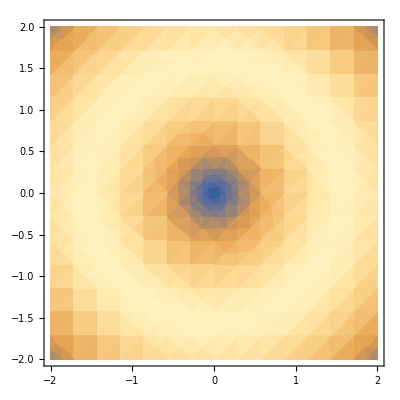

```mathematica
DensityPlot[Sin[√(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

```mathematica
DensityPlot[Sin[√(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

# 汉克儿变换推导线偏光的衍射积分

公式

-Graphics-

并不现实，因为积分式太难求

```mathematica
<<MaTeX`
<<Notation`
Symbolize[Subscript[Δf, L]]
Symbolize[Subscript[Δf, T]]
Symbolize[Subscript[z, R]]
Symbolize[Subscript[w, 0]]
Symbolize[z̃]
Symbolize[Subscript[γ, 0]]
Symbolize[Subscript[Ε, 0]]
Symbolize[Subscript[x, ∞]]
Symbolize[Subscript[y, ∞]]
Symbolize[Subscript[z, ∞]]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[θ, max]]
Symbolize[OverVector[Subscript[Ε, ∞]]]
Symbolize[OverVector[Subscript[Ε, int]]]
Symbolize[OverVector[Subscript[n, ϕ]]]
Symbolize[OverVector[Subscript[n, ρ]]]
Symbolize[OverVector[Subscript[n, θ]]]
Symbolize[Subscript[ℓ, 1]]
Symbolize[Subscript[ℓ, 2]]
Symbolize[(e⃗)_R]
Symbolize[(e⃗)_L]
Symbolize[(e⃗)_x]
Symbolize[(e⃗)_y]
Symbolize[Subscript[β, 0]]
Symbolize[Subscript[ρ, s]]
```

```mathematica
f=1;
w[0];
```

```mathematica
Notation[Subscript[Ψ, n_,m_]^(SU(2))[θ_,ϕ_,α_,β_,γ_,M_] ⟺ 1/2^(M_/2)(∑_(K=0)^M_ √Binomial[M_,K] Exp[ⅈ K γ_] (Exp[1/2 ⅈ (n_+m_) α_] ∑_(k=0)^(n_+m_) (Exp[ⅈ k α_] Subscript[d, n_,m_]^k[β] (√(2/L) (Subscript[H, k][ Cos[ϕ_] ] Subscript[H, n_+m_-k][Sin[ϕ_]] Exp[-(f Sin[θ_])^2/w[0]^2]) Exp[-ⅈ ((n_+m_-k)+k+1) ϑ[0]]))/(√(2^((n_+m_-k)+k-1) π (n_+m_-k)! k!) w[0])))]
```

Notation::expatnf: Pattern 'β' appearing in the external representation 'Notation`Private`identityForm[RowBox[{SubsuperscriptBox[Ψ,RowBox[{n_,,,m_}],RowBox[{SU,RowBox[{«3»}]}]],[,RowBox[{θ_,,,ϕ_,,,α_,,,β_,,,γ_,,,M_}],]}]]' cannot be filled since 'β' does not appear in the internal representation 'Notation`Private`identityForm[TagBox[RowBox[{FractionBox[1,SuperscriptBox[2,RowBox[{«3»}]]],RowBox[{(,RowBox[{«2»}],)}]}],HoldForm]]'.

$Failed

```mathematica
1/2^(M/2)(∑_(K=0)^M √Binomial[M,K] Exp[ⅈ K γ] (Exp[1/2 ⅈ (n+m) α] ∑_(k=0)^(n+m) (Exp[ⅈ k α] (Subscript[d, n,m]^k)[β] (√(2/L) (Subscript[H, k][ Cos[ϕ] ] Subscript[H, n+m-k][Sin[ϕ]] Exp[-(f Sin[θ])^2/w[0]^2]) Exp[-ⅈ ((n+m-k)+k+1) ϑ[0]]))/(√(2^((n+m-k)+k-1) π (n+m-k)! k!) w[0])))
```

# ML代码

基于尼康100倍油浸物选取参数，参数为：

入射光半径

```mathematica
λ=0.532;
Subscript[ρ, max]=1000λ;
```

透镜最大汇聚角

对于大NA物镜，不能认为

```mathematica
NA=1.3;
Subscript[n, 2]=1.518;
```

Solve[NA==n_2 Sin[θ_max],θ_max,InverseFunctions→True]/.Rule→Set;

结果为

```mathematica
Subscript[θ, max]=1.0282369130485443;
```

NA=1.3;
n_2=1.518;
theta_max=asin(NA/n_2)

theta_max =

    1.0282

透镜焦距

tan(θ_max)=ρ_max/f
f=ρ_max/(tan(θ_max))

化简

ρ_max/Tan[ArcSin[NA/n_2]]

结果为

误差分析

```mathematica
Subscript[n, 2]=1.518;
NA=1.3;
(*实际表达式*)
f=(√(1-(NA/Subscript[n, 2])^2)Subscript[n, 2] Subscript[ρ, max])/NA
(*杰哥的表达式*)
f=Subscript[ρ, max]/NA
```

320.75

409.231

令n_1=1计算误差

```mathematica
NA=0.95;
(*实际表达式*)
f=Subscript[ρ, max]/Tan[ArcSin[NA]]
(*杰哥的表达式*)
f=Subscript[ρ, max]/NA
```

174.86

560.

可见，杰哥所用的方式，带来的误差必然很大

%波长%
lambda=0.532;
%入瞳半径%
rho_max=1000*lambda;
%透镜焦距%
f=sqrt(1-(NA/n_2)^2)*n_2*rho_max/NA

f =

  320.7503

入射光的方位角

N_theta=151;
N_varphi=153;
theta=linspace(0,theta_max,N_theta);
varphi=linspace(0,2*pi,N_varphi);
[Theta,Varphi]=meshgrid(theta,varphi);
Rho=f*sin(Theta);
X=Rho.*cos(Varphi);
Y=Rho.*sin(Varphi);

为何此处不采用...

#### HG_21

HG_21

%束腰%
w=rho_max/3;
m=2;
n=1;

HermitePoly是厄米多项式的零点

%束腰%
w=rho_max/3;
m=2;
n=1;
Hx=polyval(HerrmitePoly(m),sqrt(2)*X/w);
Hy=polyval(HermitePoly(n),sqrt(2)*Y/w);
rc=sqrt(2^(1-n-m)/(pi*factorial(n)*factorial(m)))/w;

基变换得径向和角向分量

出瞳面上的光场分布

E_ρ=√(cos(θ))cos(θ)LP
E_φ=√(cos(θ))AP
E_z=√(cos(θ))sin(θ)LP

聚焦积分

N_xo=51;
N_yo=53;
r_max=2*lambda;
xo=linspace(-r_max,r_max,N_xo);
yo=linspace(-r_max,r_max,N_yo);
[Xo,Yo]=meshgrid(xo,yo);
R=sqrt(Xo.^2+Yo.^2);
Phi=angle(Xo+1i*Yo);

衍射积分

[m,n]=size(R);

for nn=1:n
	for mm=1:m

MATLink::errx: Error: File: C:\Users\Lee\AppData\Local\Temp\MATLink20121014292567AuqDnSdVcE\input.m Line: 5 Column: 1
     At least one END is missing: the statement may begin here.

$Failed

为何√cos(θ)是透镜

C

"☆"

## 附

输入常数C[1]

```mathematica
C[1]//FullForm
```

C[1]

polyval函数

y = polyval([3, 2, 1],[5])

y =

    86

```mathematica
x=5
3x^2+2x+1
```

5

86

求厄米多项式的零点

计算厄米多项式的个正整数值，所得矢量的元为的系数计算

function [ H ] = HermitePoly( n )
if n==0
    H=1;
elseif n==1
    H=[2 0];
else
    hpm2=zeros(1,n+1);
    hpm2(n+1)=1;
    hpm1=zeros(1,n+1);
    hpm1(n)=2;
    for k=2:n
        H=zeros(1,n+1);
        for r=n-k+1:2:n
            H(r)=2*(hpm1(r+1)-(k-1)*hpm2(r));
        end
        H(n+1)=-2*(k-1)*hpm2(n+1);
        if k<n
            hpm2=hpm1;
            hpm1=H;
        end
    end
end
end

y =

    86

所实现的功能完全同

```mathematica
HermiteH[2,√2 x/w]
```

6

```mathematica
√Cos[θ] Sin[θ] (0.25 (1+Cos[θ]) ((-0.7071067811865479-0.7071067811865471 ⅈ) ((4.7704341294471716*^-36-1.1861921016771971*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (212850788988365112429784203264000000 Cos[ϕ]-5.189288589875672*^38 (Cos[ϕ] Sin[θ])^15.)-(3.55857630503159*^-34+1.4311302388341508*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2365008766537390138108713369600000-1.5045187270650118*^37 (Cos[ϕ] Sin[θ])^15.) Sin[ϕ]+(1.1861921016771971*^-35+4.7704341294471716*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2.128507889883651*^35 Sin[ϕ]-5.1892885898756456*^38 (Sin[θ] Sin[ϕ])^15.)-(1.4311302388341506*^-34-3.5585763050315894*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) Cos[ϕ] (2.3650087665373902*^33-1.504518727064809*^37 (Sin[θ] Sin[ϕ])^15.)-(1.2455017067610605*^-33+5.008955835919544*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12-76722.68641351968 (Cos[ϕ] Sin[θ])^15.) (2.750010193648128*^31 Sin[ϕ]-6.202926930830816*^34 (Sin[θ] Sin[ϕ])^15.)+(1.0719165488867782*^-32-2.6653736524686586*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (120 Cos[ϕ]-306890.7456540787 (Cos[ϕ] Sin[θ])^15.) (3.3536709678635706*^29-2.0055245181848294*^33 (Sin[θ] Sin[ϕ])^15.)+(3.3539581674922697*^-31+1.3488402501011857*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1680-7.979159387006047*^6 (Cos[ϕ] Sin[θ])^15.) (4.299578163927655*^27 Sin[ϕ]-8.919043149492176*^30 (Sin[θ] Sin[ϕ])^15.)-(1.7767481915125941*^-31-4.417972482696709*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (30240 Cos[ϕ]-9.820503860930519*^7 (Cos[ϕ] Sin[θ])^15.) (5.810240762064398*^25-2.825827583654267*^29 (Sin[θ] Sin[ϕ])^15.)-(1.1064206828393968*^-30+4.449622434241814*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (665280-9.218997999448525*^8 (Cos[ϕ] Sin[θ])^15.) (8.300343945806283*^23 Sin[ϕ]-1.6070960602105548*^27 (Sin[θ] Sin[ϕ])^15.)-(1.836784105031688*^-30-4.5672547586927864*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17297280 Cos[ϕ]-5.340881024767063*^10 (Cos[ϕ] Sin[θ])^15.) (1.2576278705767096*^22-3.948198339651211*^25 (Sin[θ] Sin[ϕ])^15.)-(1.663598836839213*^-29+6.690390753525752*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (518918400+5.001189796217476*^11 (Cos[ϕ] Sin[θ])^15.) (2.0284320493172736*^20 Sin[ϕ]-3.834721717179024*^23 (Sin[θ] Sin[ϕ])^15.)+(4.312138522631156*^-30-1.0722346264690624*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17643225600 Cos[ϕ]-4.6860144735063164*^13 (Cos[ϕ] Sin[θ])^15.) (3.49729663675392*^18-3.94213700914298*^21 (Sin[θ] Sin[ϕ])^15.)-(1.6903949164161497*^-30+6.798154860510161*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (670442572800+1.0471973107085615*^15 (Cos[ϕ] Sin[θ])^15.) (6.476475253248*^16 Sin[ϕ]-1.2856207705060675*^20 (Sin[θ] Sin[ϕ])^15.)+(3.823512310941183*^-29+1.53767788511535*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1295295050649600+8.516867869297705*^17 (Cos[ϕ] Sin[θ])^15.) (2.81585880576*^13 Sin[ϕ]-6.329444534005149*^16 (Sin[θ] Sin[ϕ])^15.)+(9.711649800728544*^-30-2.4148498805944363*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1295295050649600 Cos[ϕ]+2.713863554676381*^18 (Cos[ϕ] Sin[θ])^15.) (-2.81585880576*^13-3.5546020142942244*^16 (Sin[θ] Sin[ϕ])^15.)+(1.0722346264690692*^-29+4.312138522631183*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3497296636753920000-3.9421370091431374*^21 (Cos[ϕ] Sin[θ])^15.) (1.76432256*^10 Sin[ϕ]-4.6860144735063164*^13 (Sin[θ] Sin[ϕ])^15.)-(7.185514111821071*^-30-1.7867137150722882*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-3497296636753920000 Cos[ϕ]+6.70692674463598*^21 (Cos[ϕ] Sin[θ])^15.) (-1.76432256*^10-2.6122105712779336*^13 (Sin[θ] Sin[ϕ])^15.)-(4.567254758692786*^-30+1.8367841050316875*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12576278705767096320000-3.948198339650954*^25 (Cos[ϕ] Sin[θ])^15.) (1.729728*^7 Sin[ϕ]-5.340881024767063*^10 (Sin[θ] Sin[ϕ])^15.)-(4.449622434241868*^-31-1.1064206828394101*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (830034394580628357120000 Cos[ϕ]-1.6070960602105774*^27 (Cos[ϕ] Sin[θ])^15.) (665280.-9.218997999448525*^8 (Sin[θ] Sin[ϕ])^15.)-(4.41797248269672*^-31+1.776748191512599*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (58102407620643984998400000-2.825827583654451*^29 (Cos[ϕ] Sin[θ])^15.) (30240. Sin[ϕ]-9.820503860930519*^7 (Sin[θ] Sin[ϕ])^15.)+(1.3488402501011868*^-31-3.3539581674922723*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (4299578163927654889881600000 Cos[ϕ]-8.919043149492264*^30 (Cos[ϕ] Sin[θ])^15.) (1680.-7.979159387006047*^6 (Sin[θ] Sin[ϕ])^15.)+(2.6653736524686597*^-32+1.0719165488867786*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (335367096786357081410764800000-2.0055245181851608*^33 (Cos[ϕ] Sin[θ])^15.) (120. Sin[ϕ]-306890.7456540787 (Sin[θ] Sin[ϕ])^15.)-(5.0089558359195055*^-34-1.2455017067610509*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (27500101936481280675682713600000 Cos[ϕ]-6.202926930830702*^34 (Cos[ϕ] Sin[θ])^15.) (12.-76722.68641351968 (Sin[θ] Sin[ϕ])^15.)-(4.293390716502455*^-34-1.0675728915094775*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2365008766537390138108713369600000 Cos[ϕ]+5.554982777798487*^36 (Cos[ϕ] Sin[θ])^15.) (-2.+9590.33580168996 (Sin[θ] Sin[ϕ])^15.)+(2.7282418338575524*^-33+1.0971998497728492*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-27500101936481280675682713600000+1.722620779503491*^35 (Cos[ϕ] Sin[θ])^15.) (-12. Sin[ϕ]+19180.67160337992 (Sin[θ] Sin[ϕ])^15.)+(2.3375127234291136*^-32-5.812341298218265*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-335367096786357081410764800000 Cos[ϕ]+7.252277533992086*^32 (Cos[ϕ] Sin[θ])^15.) (-120.+728865.520928437 (Sin[θ] Sin[ϕ])^15.)+(2.775689517924625*^-32+1.1162815862906317*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-4299578163927654889881600000+2.36902370188983*^31 (Cos[ϕ] Sin[θ])^15.) (-1680. Sin[ϕ]+5.140419989705819*^6 (Sin[θ] Sin[ϕ])^15.)+(2.325586638105487*^-31-5.782686495676312*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-58102407620643984998400000 Cos[ϕ]+1.1602607823279685*^29 (Cos[ϕ] Sin[θ])^15.) (-30240.+9.222066906905065*^7 (Sin[θ] Sin[ϕ])^15.)-(3.0168225434623907*^-30-7.501478851006594*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12576278705767096320000 Cos[ϕ]+2.387706395964935*^25 (Cos[ϕ] Sin[θ])^15.) (-1.729728*^7+9.513613115276441*^7 (Sin[θ] Sin[ϕ])^15.)-(2.234430061929335*^-30+8.986066769639632*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-830034394580628357120000+3.371773069238801*^27 (Cos[ϕ] Sin[θ])^15.) (-665280. Sin[ϕ]+2.148542110324205*^9 (Sin[θ] Sin[ϕ])^15.)-(6.690390753525759*^-30-1.6635988368392146*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (202843204931727360000 Cos[ϕ]-3.834721717179012*^23 (Cos[ϕ] Sin[θ])^15.) (5.189184*^8+5.001189796217476*^11 (Sin[θ] Sin[ϕ])^15.)-(2.2419979675380185*^-30+9.016502139385438*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-202843204931727360000+4.343668282876388*^23 (Cos[ϕ] Sin[θ])^15.) (-5.189184*^8 Sin[ϕ]+1.495636959197083*^12 (Sin[θ] Sin[ϕ])^15.)-(6.7981548605097765*^-31-1.690394916416054*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (64764752532480000 Cos[ϕ]-1.2856207705060675*^20 (Cos[ϕ] Sin[θ])^15.) (6.704425728*^11+1.0471973107085615*^15 (Sin[θ] Sin[ϕ])^15.)+(2.990698698274645*^-29+1.2027504753209957*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-64764752532480000+1.0849369002214711*^19 (Cos[ϕ] Sin[θ])^15.) (-6.704425728*^11 Sin[ϕ]+1.6347209990367152*^15 (Sin[θ] Sin[ϕ])^15.)+(1.5376778851153507*^-29-3.823512310941185*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (28158588057600 Cos[ϕ]-6.329444534005149*^16 (Cos[ϕ] Sin[θ])^15.) (1.2952950506496*^15+8.516867869297705*^17 (Sin[θ] Sin[ϕ])^15.)+(2.4148498805944274*^-29+9.711649800728511*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-28158588057600-3.5546020142942244*^16 (Cos[ϕ] Sin[θ])^15.) (-1.2952950506496*^15 Sin[ϕ]+2.713863554676381*^18 (Sin[θ] Sin[ϕ])^15.)+(1.2027504753209923*^-29-2.990698698274637*^-29 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-670442572800 Cos[ϕ]+1.6347209990367152*^15 (Cos[ϕ] Sin[θ])^15.) (-6.476475253248*^16+1.0849369002214711*^19 (Sin[θ] Sin[ϕ])^15.)-(1.7867137150722936*^-29+7.185514111821092*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17643225600-2.6122105712779336*^13 (Cos[ϕ] Sin[θ])^15.) (-3.49729663675392*^18 Sin[ϕ]+6.70692674463598*^21 (Sin[θ] Sin[ϕ])^15.)-(9.016502139385541*^-31-2.2419979675380445*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-518918400 Cos[ϕ]+1.495636959197083*^12 (Cos[ϕ] Sin[θ])^15.) (-2.0284320493172736*^20+4.34366828287612*^23 (Sin[θ] Sin[ϕ])^15.)-(7.501478851006564*^-30+3.0168225434623788*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17297280+9.513613115276441*^7 (Cos[ϕ] Sin[θ])^15.) (-1.2576278705767096*^22 Sin[ϕ]+2.38770639596492*^25 (Sin[θ] Sin[ϕ])^15.)-(8.986066769639614*^-31-2.234430061929331*^-30 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-665280 Cos[ϕ]+2.148542110324205*^9 (Cos[ϕ] Sin[θ])^15.) (-8.300343945806283*^23+3.371773069238715*^27 (Sin[θ] Sin[ϕ])^15.)+(5.7826864956763355*^-31+2.325586638105496*^-31 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-30240+9.222066906905065*^7 (Cos[ϕ] Sin[θ])^15.) (-5.810240762064398*^25 Sin[ϕ]+1.1602607823279351*^29 (Sin[θ] Sin[ϕ])^15.)+(1.1162815862906426*^-32-2.7756895179246523*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1680 Cos[ϕ]+5.140419989705819*^6 (Cos[ϕ] Sin[θ])^15.) (-4.299578163927655*^27+2.3690237018900563*^31 (Sin[θ] Sin[ϕ])^15.)+(5.812341298218252*^-32+2.3375127234291084*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-120+728865.520928437 (Cos[ϕ] Sin[θ])^15.) (-3.3536709678635706*^29 Sin[ϕ]+7.25227753399186*^32 (Sin[θ] Sin[ϕ])^15.)+(1.097199849772848*^-33-2.7282418338575496*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12 Cos[ϕ]+19180.67160337992 (Cos[ϕ] Sin[θ])^15.) (-2.750010193648128*^31+1.7226207795035238*^35 (Sin[θ] Sin[ϕ])^15.)-(1.067572891509477*^-33+4.293390716502452*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2+9590.33580168996 (Cos[ϕ] Sin[θ])^15.) (-2.3650087665373902*^33 Sin[ϕ]+5.55498277779848*^36 (Sin[θ] Sin[ϕ])^15.))-(1.4142135623730892-1.414213562373101 ⅈ) ((1.850108777613364*^-40-4.60038721785267*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1960781468160819415703172080467968000000 Cos[ϕ]-5.081410612980245*^42 (Cos[ϕ] Sin[θ])^15.)-(1.9321626314981202*^-38+7.770456865976124*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (20007974164906320568399715106816000000-1.2077648208967424*^41 (Cos[ϕ] Sin[θ])^15.) Sin[ϕ]-(4.60038721785267*^-40+1.850108777613364*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1.9607814681608194*^39 Sin[ϕ]-5.081410612980464*^42 (Sin[θ] Sin[ϕ])^15.)+(7.770456865976123*^-39-1.9321626314981197*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) Cos[ϕ] (2.0007974164906321*^37-1.2077648208968575*^41 (Sin[θ] Sin[ϕ])^15.)-(1.4426814315185943*^-36+5.801941126595498*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12-76722.68641351968 (Cos[ϕ] Sin[θ])^15.) (2.128507889883651*^35 Sin[ϕ]-5.1892885898756456*^38 (Sin[θ] Sin[ϕ])^15.)+(6.7343959505126125*^-37-1.6745409472983633*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (120 Cos[ϕ]-306890.7456540787 (Cos[ϕ] Sin[θ])^15.) (2.3650087665373902*^33-1.504518727064809*^37 (Sin[θ] Sin[ϕ])^15.)+(4.002796918253598*^-35+1.609779647401384*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1680-7.979159387006047*^6 (Cos[ϕ] Sin[θ])^15.) (2.750010193648128*^31 Sin[ϕ]-6.202926930830816*^34 (Sin[θ] Sin[ϕ])^15.)+(1.0114544687212286*^-35-2.5150316920000603*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (30240 Cos[ϕ]-9.820503860930519*^7 (Cos[ϕ] Sin[θ])^15.) (3.3536709678635706*^29-2.0055245181848294*^33 (Sin[θ] Sin[ϕ])^15.)+(1.4032653138360397*^-34+5.643423806529614*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (665280-9.218997999448525*^8 (Cos[ϕ] Sin[θ])^15.) (4.299578163927655*^27 Sin[ϕ]-8.919043149492176*^30 (Sin[θ] Sin[ϕ])^15.)-(4.704959829302764*^-34-1.1699115922878998*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17297280 Cos[ϕ]-5.340881024767063*^10 (Cos[ϕ] Sin[θ])^15.) (5.810240762064398*^25-2.825827583654267*^29 (Sin[θ] Sin[ϕ])^15.)-(4.169623060128195*^-33+1.6768710670583655*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (518918400+5.001189796217476*^11 (Cos[ϕ] Sin[θ])^15.) (8.300343945806283*^23 Sin[ϕ]-1.6070960602105548*^27 (Sin[θ] Sin[ϕ])^15.)+(1.3715180137483867*^-33-3.410347551370475*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17643225600 Cos[ϕ]-4.6860144735063164*^13 (Cos[ϕ] Sin[θ])^15.) (1.2576278705767096*^22-3.948198339651211*^25 (Sin[θ] Sin[ϕ])^15.)+(4.603287301954777*^-33+1.851275086186761*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (670442572800+1.0471973107085615*^15 (Cos[ϕ] Sin[θ])^15.) (2.0284320493172736*^20 Sin[ϕ]-3.834721717179024*^23 (Sin[θ] Sin[ϕ])^15.)+(3.7762377848553425*^-33-9.389802506331999*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (28158588057600 Cos[ϕ]-6.329444534005149*^16 (Cos[ϕ] Sin[θ])^15.) (3.49729663675392*^18-3.94213700914298*^21 (Sin[θ] Sin[ϕ])^15.)+(1.490358188505021*^-32+5.993679739915751*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1295295050649600+8.516867869297705*^17 (Cos[ϕ] Sin[θ])^15.) (6.476475253248*^16 Sin[ϕ]-1.2856207705060675*^20 (Sin[θ] Sin[ϕ])^15.)-(9.389802506331981*^-33+3.776237784855335*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3497296636753920000-3.9421370091431374*^21 (Cos[ϕ] Sin[θ])^15.) (2.81585880576*^13 Sin[ϕ]-6.329444534005149*^16 (Sin[θ] Sin[ϕ])^15.)-(6.044907771880843*^-33-1.503096292680278*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-3497296636753920000 Cos[ϕ]+6.70692674463598*^21 (Cos[ϕ] Sin[θ])^15.) (-2.81585880576*^13-3.5546020142942244*^16 (Sin[θ] Sin[ϕ])^15.)-(3.410347551370497*^-33+1.3715180137483956*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12576278705767096320000-3.948198339650954*^25 (Cos[ϕ] Sin[θ])^15.) (1.76432256*^10 Sin[ϕ]-4.6860144735063164*^13 (Sin[θ] Sin[ϕ])^15.)+(1.4741592735672111*^-33-3.6655701336361186*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12576278705767096320000 Cos[ϕ]+2.387706395964935*^25 (Cos[ϕ] Sin[θ])^15.) (-1.76432256*^10-2.6122105712779336*^13 (Sin[θ] Sin[ϕ])^15.)+(1.1699115922879005*^-33+4.704959829302766*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (58102407620643984998400000-2.825827583654451*^29 (Cos[ϕ] Sin[θ])^15.) (1.729728*^7 Sin[ϕ]-5.340881024767063*^10 (Sin[θ] Sin[ϕ])^15.)-(5.643423806529561*^-35-1.4032653138360264*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (4299578163927654889881600000 Cos[ϕ]-8.919043149492264*^30 (Cos[ϕ] Sin[θ])^15.) (665280.-9.218997999448525*^8 (Sin[θ] Sin[ϕ])^15.)-(2.5150316920000416*^-35+1.0114544687212211*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (335367096786357081410764800000-2.0055245181851608*^33 (Cos[ϕ] Sin[θ])^15.) (30240. Sin[ϕ]-9.820503860930519*^7 (Sin[θ] Sin[ϕ])^15.)-(1.6097796474013886*^-35-4.002796918253609*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (27500101936481280675682713600000 Cos[ϕ]-6.202926930830702*^34 (Cos[ϕ] Sin[θ])^15.) (1680.-7.979159387006047*^6 (Sin[θ] Sin[ϕ])^15.)-(1.674540947298377*^-36+6.734395950512668*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2365008766537390138108713369600000-1.5045187270650118*^37 (Cos[ϕ] Sin[θ])^15.) (120. Sin[ϕ]-306890.7456540787 (Sin[θ] Sin[ϕ])^15.)+(5.801941126595512*^-37-1.4426814315185978*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (212850788988365112429784203264000000 Cos[ϕ]-5.189288589875672*^38 (Cos[ϕ] Sin[θ])^15.) (12.-76722.68641351968 (Sin[θ] Sin[ϕ])^15.)-(3.6262132041221935*^-38-9.016758946991231*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-20007974164906320568399715106816000000 Cos[ϕ]+5.0415183841676*^40 (Cos[ϕ] Sin[θ])^15.) (-2.+9590.33580168996 (Sin[θ] Sin[ϕ])^15.)+(4.766001157695367*^-37+1.9167126936074455*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-212850788988365112429784203264000000+1.3368644074099131*^39 (Cos[ϕ] Sin[θ])^15.) (-12. Sin[ϕ]+19180.67160337992 (Sin[θ] Sin[ϕ])^15.)+(1.9944172622672024*^-36-4.959217420845167*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2365008766537390138108713369600000 Cos[ϕ]+5.554982777798487*^36 (Cos[ϕ] Sin[θ])^15.) (-120.+728865.520928437 (Sin[θ] Sin[ϕ])^15.)-(2.540333821698242*^-35+1.0216300669980989*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-27500101936481280675682713600000+1.722620779503491*^35 (Cos[ϕ] Sin[θ])^15.) (-1680. Sin[ϕ]+5.140419989705819*^6 (Sin[θ] Sin[ϕ])^15.)-(8.72415093866026*^-35-2.1693033918039887*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-335367096786357081410764800000 Cos[ϕ]+7.252277533992086*^32 (Cos[ϕ] Sin[θ])^15.) (-30240.+9.222066906905065*^7 (Sin[θ] Sin[ϕ])^15.)+(5.5659634522284786*^-34-1.3840044126323292*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-58102407620643984998400000 Cos[ϕ]+1.1602607823279685*^29 (Cos[ϕ] Sin[θ])^15.) (-1.729728*^7+9.513613115276441*^7 (Sin[θ] Sin[ϕ])^15.)+(3.226840405443962*^-34+1.297718099663787*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-4299578163927654889881600000+2.36902370188983*^31 (Cos[ϕ] Sin[θ])^15.) (-665280. Sin[ϕ]+2.148542110324205*^9 (Sin[θ] Sin[ϕ])^15.)+(1.6768710670583672*^-33-4.169623060128199*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (830034394580628357120000 Cos[ϕ]-1.6070960602105774*^27 (Cos[ϕ] Sin[θ])^15.) (5.189184*^8+5.001189796217476*^11 (Sin[θ] Sin[ϕ])^15.)+(8.701816438056982*^-34+3.499554757206761*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-830034394580628357120000+3.371773069238801*^27 (Cos[ϕ] Sin[θ])^15.) (-5.189184*^8 Sin[ϕ]+1.495636959197083*^12 (Sin[θ] Sin[ϕ])^15.)-(1.8512750861867722*^-33-4.603287301954804*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (202843204931727360000 Cos[ϕ]-3.834721717179012*^23 (Cos[ϕ] Sin[θ])^15.) (6.704425728*^11+1.0471973107085615*^15 (Sin[θ] Sin[ϕ])^15.)-(9.795162865800756*^-33+3.939259009729478*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-202843204931727360000+4.343668282876388*^23 (Cos[ϕ] Sin[θ])^15.) (-6.704425728*^11 Sin[ϕ]+1.6347209990367152*^15 (Sin[θ] Sin[ϕ])^15.)-(5.99367973991574*^-33-1.4903581885050186*^-32 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (64764752532480000 Cos[ϕ]-1.2856207705060675*^20 (Cos[ϕ] Sin[θ])^15.) (1.2952950506496*^15+8.516867869297705*^17 (Sin[θ] Sin[ϕ])^15.)+(2.2928587515462067*^-33+9.22104575371662*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-64764752532480000+1.0849369002214711*^19 (Cos[ϕ] Sin[θ])^15.) (-1.2952950506496*^15 Sin[ϕ]+2.713863554676381*^18 (Sin[θ] Sin[ϕ])^15.)-(9.221045753716432*^-34-2.29285875154616*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1295295050649600 Cos[ϕ]+2.713863554676381*^18 (Cos[ϕ] Sin[θ])^15.) (-6.476475253248*^16+1.0849369002214711*^19 (Sin[θ] Sin[ϕ])^15.)+(1.5030962926802745*^-32+6.044907771880829*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-28158588057600-3.5546020142942244*^16 (Cos[ϕ] Sin[θ])^15.) (-3.49729663675392*^18 Sin[ϕ]+6.70692674463598*^21 (Sin[θ] Sin[ϕ])^15.)+(3.939259009729472*^-33-9.795162865800744*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-670442572800 Cos[ϕ]+1.6347209990367152*^15 (Cos[ϕ] Sin[θ])^15.) (-2.0284320493172736*^20+4.34366828287612*^23 (Sin[θ] Sin[ϕ])^15.)-(3.665570133636134*^-33+1.4741592735672173*^-33 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17643225600-2.6122105712779336*^13 (Cos[ϕ] Sin[θ])^15.) (-1.2576278705767096*^22 Sin[ϕ]+2.38770639596492*^25 (Sin[θ] Sin[ϕ])^15.)-(3.49955475720678*^-34-8.70181643805703*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-518918400 Cos[ϕ]+1.495636959197083*^12 (Cos[ϕ] Sin[θ])^15.) (-8.300343945806283*^23+3.371773069238715*^27 (Sin[θ] Sin[ϕ])^15.)-(1.3840044126323246*^-33+5.56596345222846*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17297280+9.513613115276441*^7 (Cos[ϕ] Sin[θ])^15.) (-5.810240762064398*^25 Sin[ϕ]+1.1602607823279351*^29 (Sin[θ] Sin[ϕ])^15.)-(1.2977180996637823*^-34-3.226840405443951*^-34 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-665280 Cos[ϕ]+2.148542110324205*^9 (Cos[ϕ] Sin[θ])^15.) (-4.299578163927655*^27+2.3690237018900563*^31 (Sin[θ] Sin[ϕ])^15.)+(2.1693033918039857*^-34+8.724150938660247*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-30240+9.222066906905065*^7 (Cos[ϕ] Sin[θ])^15.) (-3.3536709678635706*^29 Sin[ϕ]+7.25227753399186*^32 (Sin[θ] Sin[ϕ])^15.)+(1.0216300669980981*^-35-2.54033382169824*^-35 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1680 Cos[ϕ]+5.140419989705819*^6 (Cos[ϕ] Sin[θ])^15.) (-2.750010193648128*^31+1.7226207795035238*^35 (Sin[θ] Sin[ϕ])^15.)-(4.9592174208451786*^-36+1.9944172622672068*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-120+728865.520928437 (Cos[ϕ] Sin[θ])^15.) (-2.3650087665373902*^33 Sin[ϕ]+5.55498277779848*^36 (Sin[θ] Sin[ϕ])^15.)-(1.9167126936074418*^-37-4.766001157695358*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12 Cos[ϕ]+19180.67160337992 (Cos[ϕ] Sin[θ])^15.) (-2.128507889883651*^35+1.3368644074101866*^39 (Sin[θ] Sin[ϕ])^15.)+(9.016758946991224*^-38+3.6262132041221904*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2+9590.33580168996 (Cos[ϕ] Sin[θ])^15.) (-2.0007974164906321*^37 Sin[ϕ]+5.041518384167491*^40 (Sin[θ] Sin[ϕ])^15.))+(1.7320508075688783+1.7320508075688759 ⅈ) ((4.868947468072667*^-45-1.2106879318294427*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (21199969233754779522582696534019670016000000 Cos[ϕ]-5.720669285828024*^46 (Cos[ϕ] Sin[θ])^15.)-(6.537714831878992*^-43+2.62923163275924*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (199999709752403580401723552207732736000000-1.0281540025883455*^45 (Cos[ϕ] Sin[θ])^15.) Sin[ϕ]+(1.2106879318294427*^-44+4.868947468072667*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2.1199969233754778*^43 Sin[ϕ]-5.720669285828082*^46 (Sin[θ] Sin[ϕ])^15.)-(2.6292316327592406*^-43-6.5377148318789916*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) Cos[ϕ] (1.9999970975240357*^41-1.0281540025882896*^45 (Sin[θ] Sin[ϕ])^15.)+(1.5817637829351645*^-40+6.36127986703693*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12-76722.68641351968 (Cos[ϕ] Sin[θ])^15.) (1.9607814681608194*^39 Sin[ϕ]-5.081410612980464*^42 (Sin[θ] Sin[ϕ])^15.)-(2.1818240499180366*^-40-5.425213691320902*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (120 Cos[ϕ]-306890.7456540787 (Cos[ϕ] Sin[θ])^15.) (2.0007974164906321*^37-1.2077648208968575*^41 (Sin[θ] Sin[ϕ])^15.)-(4.344263078266314*^-39+1.747104944178642*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1680-7.979159387006047*^6 (Cos[ϕ] Sin[θ])^15.) (2.128507889883651*^35 Sin[ϕ]-5.1892885898756456*^38 (Sin[θ] Sin[ϕ])^15.)+(6.70877664783327*^-39-1.66817058062983*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (30240 Cos[ϕ]-9.820503860930519*^7 (Cos[ϕ] Sin[θ])^15.) (2.3650087665373902*^33-1.504518727064809*^37 (Sin[θ] Sin[ϕ])^15.)+(1.0069744326311966*^-37+4.049685707831337*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (665280-9.218997999448525*^8 (Cos[ϕ] Sin[θ])^15.) (2.750010193648128*^31 Sin[ϕ]-6.202926930830816*^34 (Sin[θ] Sin[ϕ])^15.)-(7.870771410668171*^-38-1.957106340450239*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17297280 Cos[ϕ]-5.340881024767063*^10 (Cos[ϕ] Sin[θ])^15.) (3.3536709678635706*^29-2.0055245181848294*^33 (Sin[θ] Sin[ϕ])^15.)-(8.31172484112847*^-37+3.3426740745137222*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (518918400+5.001189796217476*^11 (Cos[ϕ] Sin[θ])^15.) (4.299578163927655*^27 Sin[ϕ]-8.919043149492176*^30 (Sin[θ] Sin[ϕ])^15.)+(1.9529869758713167*^-37-4.8561989592453614*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17643225600 Cos[ϕ]-4.6860144735063164*^13 (Cos[ϕ] Sin[θ])^15.) (5.810240762064398*^25-2.825827583654267*^29 (Sin[θ] Sin[ϕ])^15.)+(1.407232596683819*^-36+5.659378778360742*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (670442572800+1.0471973107085615*^15 (Cos[ϕ] Sin[θ])^15.) (8.300343945806283*^23 Sin[ϕ]-1.6070960602105548*^27 (Sin[θ] Sin[ϕ])^15.)+(7.783352526315854*^-37-1.935369201367644*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (28158588057600 Cos[ϕ]-6.329444534005149*^16 (Cos[ϕ] Sin[θ])^15.) (1.2576278705767096*^22-3.948198339651211*^25 (Sin[θ] Sin[ϕ])^15.)+(2.8992423808923167*^-36+1.1659700636846904*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1295295050649600+8.516867869297705*^17 (Cos[ϕ] Sin[θ])^15.) (2.0284320493172736*^20 Sin[ϕ]-3.834721717179024*^23 (Sin[θ] Sin[ϕ])^15.)-(2.5012453694934535*^-36-6.219470641749804*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (64764752532480000 Cos[ϕ]-1.2856207705060675*^20 (Cos[ϕ] Sin[θ])^15.) (3.49729663675392*^18-3.94213700914298*^21 (Sin[θ] Sin[ϕ])^15.)-(6.219470641749807*^-36+2.5012453694934545*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3497296636753920000-3.9421370091431374*^21 (Cos[ϕ] Sin[θ])^15.) (6.476475253248*^16 Sin[ϕ]-1.2856207705060675*^20 (Sin[θ] Sin[ϕ])^15.)+(1.9353692013676354*^-36+7.78335252631582*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12576278705767096320000-3.948198339650954*^25 (Cos[ϕ] Sin[θ])^15.) (2.81585880576*^13 Sin[ϕ]-6.329444534005149*^16 (Sin[θ] Sin[ϕ])^15.)+(1.8041364449837847*^-36-4.486074733067838*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12576278705767096320000 Cos[ϕ]+2.387706395964935*^25 (Cos[ϕ] Sin[θ])^15.) (-2.81585880576*^13-3.5546020142942244*^16 (Sin[θ] Sin[ϕ])^15.)+(4.856198959245401*^-37+1.952986975871332*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (58102407620643984998400000-2.825827583654451*^29 (Cos[ϕ] Sin[θ])^15.) (1.76432256*^10 Sin[ϕ]-4.6860144735063164*^13 (Sin[θ] Sin[ϕ])^15.)-(3.941571800471225*^-37-9.800913734562686*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-58102407620643984998400000 Cos[ϕ]+1.1602607823279685*^29 (Cos[ϕ] Sin[θ])^15.) (-1.76432256*^10-2.6122105712779336*^13 (Sin[θ] Sin[ϕ])^15.)-(1.9571063404502436*^-37+7.87077141066819*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (335367096786357081410764800000-2.0055245181851608*^33 (Cos[ϕ] Sin[θ])^15.) (1.729728*^7 Sin[ϕ]-5.340881024767063*^10 (Sin[θ] Sin[ϕ])^15.)+(4.0496857078313386*^-38-1.0069744326311968*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (27500101936481280675682713600000 Cos[ϕ]-6.202926930830702*^34 (Cos[ϕ] Sin[θ])^15.) (665280.-9.218997999448525*^8 (Sin[θ] Sin[ϕ])^15.)+(1.6681705806298344*^-38+6.708776647833287*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2365008766537390138108713369600000-1.5045187270650118*^37 (Cos[ϕ] Sin[θ])^15.) (30240. Sin[ϕ]-9.820503860930519*^7 (Sin[θ] Sin[ϕ])^15.)-(1.7471049441786417*^-39-4.344263078266313*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (212850788988365112429784203264000000 Cos[ϕ]-5.189288589875672*^38 (Cos[ϕ] Sin[θ])^15.) (1680.-7.979159387006047*^6 (Sin[θ] Sin[ϕ])^15.)-(5.4252136913209225*^-40+2.1818240499180448*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (20007974164906320568399715106816000000-1.2077648208967424*^41 (Cos[ϕ] Sin[θ])^15.) (120. Sin[ϕ]-306890.7456540787 (Sin[θ] Sin[ϕ])^15.)+(6.361279867036944*^-41-1.581763782935168*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1960781468160819415703172080467968000000 Cos[ϕ]-5.081410612980245*^42 (Cos[ϕ] Sin[θ])^15.) (12.-76722.68641351968 (Sin[θ] Sin[ϕ])^15.)-(1.645704244208562*^-42-4.092125209583518*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-199999709752403580401723552207732736000000 Cos[ϕ]+5.302921620490725*^44 (Cos[ϕ] Sin[θ])^15.) (-2.+9590.33580168996 (Sin[θ] Sin[ϕ])^15.)+(3.1163107365289875*^-41+1.2532670782819052*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1960781468160819415703172080467968000000+1.1075550375524041*^43 (Cos[ϕ] Sin[θ])^15.) (-12. Sin[ϕ]+19180.67160337992 (Sin[θ] Sin[ϕ])^15.)-(4.623162999884366*^-40-1.1495724050306941*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-20007974164906320568399715106816000000 Cos[ϕ]+5.0415183841676*^40 (Cos[ϕ] Sin[θ])^15.) (-120.+728865.520928437 (Sin[θ] Sin[ϕ])^15.)+(7.139184596411912*^-40+2.8711209429731115*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-212850788988365112429784203264000000+1.3368644074099131*^39 (Cos[ϕ] Sin[θ])^15.) (-1680. Sin[ϕ]+5.140419989705819*^6 (Sin[θ] Sin[ϕ])^15.)+(1.0251724700345996*^-38-2.5491421824807147*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2365008766537390138108713369600000 Cos[ϕ]+5.554982777798487*^36 (Cos[ϕ] Sin[θ])^15.) (-30240.+9.222066906905065*^7 (Sin[θ] Sin[ϕ])^15.)-(3.319551004782593*^-38-8.254228181626801*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-335367096786357081410764800000 Cos[ϕ]+7.252277533992086*^32 (Cos[ϕ] Sin[θ])^15.) (-1.729728*^7+9.513613115276441*^7 (Sin[θ] Sin[ϕ])^15.)+(4.1569696552122477*^-39+1.6717823268475367*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-27500101936481280675682713600000+1.722620779503491*^35 (Cos[ϕ] Sin[θ])^15.) (-665280. Sin[ϕ]+2.148542110324205*^9 (Sin[θ] Sin[ϕ])^15.)-(3.3426740745137264*^-37-8.31172484112848*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (4299578163927654889881600000 Cos[ϕ]-8.919043149492264*^30 (Cos[ϕ] Sin[θ])^15.) (5.189184*^8+5.001189796217476*^11 (Sin[θ] Sin[ϕ])^15.)-(3.733189168507822*^-37+1.5013531953173155*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-4299578163927654889881600000+2.36902370188983*^31 (Cos[ϕ] Sin[θ])^15.) (-5.189184*^8 Sin[ϕ]+1.495636959197083*^12 (Sin[θ] Sin[ϕ])^15.)+(5.659378778360768*^-37-1.4072325966838257*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (830034394580628357120000 Cos[ϕ]-1.6070960602105774*^27 (Cos[ϕ] Sin[θ])^15.) (6.704425728*^11+1.0471973107085615*^15 (Sin[θ] Sin[ϕ])^15.)+(2.3128833335054014*^-36+9.301577354952147*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-830034394580628357120000+3.371773069238801*^27 (Cos[ϕ] Sin[θ])^15.) (-6.704425728*^11 Sin[ϕ]+1.6347209990367152*^15 (Sin[θ] Sin[ϕ])^15.)+(1.1659700636846857*^-36-2.899242380892305*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (202843204931727360000 Cos[ϕ]-3.834721717179012*^23 (Cos[ϕ] Sin[θ])^15.) (1.2952950506496*^15+8.516867869297705*^17 (Sin[θ] Sin[ϕ])^15.)-(2.5735740586550982*^-36+1.0349980839283282*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-202843204931727360000+4.343668282876388*^23 (Cos[ϕ] Sin[θ])^15.) (-1.2952950506496*^15 Sin[ϕ]+2.713863554676381*^18 (Sin[θ] Sin[ϕ])^15.)-(1.296942043441053*^-36-3.2249107031295355*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-3497296636753920000 Cos[ϕ]+6.70692674463598*^21 (Cos[ϕ] Sin[θ])^15.) (-6.476475253248*^16+1.0849369002214711*^19 (Sin[θ] Sin[ϕ])^15.)-(3.2249107031295195*^-36+1.2969420434410467*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-64764752532480000+1.0849369002214711*^19 (Cos[ϕ] Sin[θ])^15.) (-3.49729663675392*^18 Sin[ϕ]+6.70692674463598*^21 (Sin[θ] Sin[ϕ])^15.)-(1.0349980839283236*^-36-2.5735740586550868*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1295295050649600 Cos[ϕ]+2.713863554676381*^18 (Cos[ϕ] Sin[θ])^15.) (-2.0284320493172736*^20+4.34366828287612*^23 (Sin[θ] Sin[ϕ])^15.)+(4.486074733067837*^-36+1.8041364449837843*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-28158588057600-3.5546020142942244*^16 (Cos[ϕ] Sin[θ])^15.) (-1.2576278705767096*^22 Sin[ϕ]+2.38770639596492*^25 (Sin[θ] Sin[ϕ])^15.)+(9.30157735495214*^-37-2.3128833335053998*^-36 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-670442572800 Cos[ϕ]+1.6347209990367152*^15 (Cos[ϕ] Sin[θ])^15.) (-8.300343945806283*^23+3.371773069238715*^27 (Sin[θ] Sin[ϕ])^15.)-(9.800913734562694*^-37+3.941571800471229*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17643225600-2.6122105712779336*^13 (Cos[ϕ] Sin[θ])^15.) (-5.810240762064398*^25 Sin[ϕ]+1.1602607823279351*^29 (Sin[θ] Sin[ϕ])^15.)-(1.5013531953173176*^-37-3.733189168507827*^-37 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-518918400 Cos[ϕ]+1.495636959197083*^12 (Cos[ϕ] Sin[θ])^15.) (-4.299578163927655*^27+2.3690237018900563*^31 (Sin[θ] Sin[ϕ])^15.)-(8.25422818162671*^-38+3.3195510047825565*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17297280+9.513613115276441*^7 (Cos[ϕ] Sin[θ])^15.) (-3.3536709678635706*^29 Sin[ϕ]+7.25227753399186*^32 (Sin[θ] Sin[ϕ])^15.)+(1.6717823268475782*^-39-4.156969655212351*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-665280 Cos[ϕ]+2.148542110324205*^9 (Cos[ϕ] Sin[θ])^15.) (-2.750010193648128*^31+1.7226207795035238*^35 (Sin[θ] Sin[ϕ])^15.)+(2.549142182480701*^-38+1.0251724700345944*^-38 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-30240+9.222066906905065*^7 (Cos[ϕ] Sin[θ])^15.) (-2.3650087665373902*^33 Sin[ϕ]+5.55498277779848*^36 (Sin[θ] Sin[ϕ])^15.)+(2.8711209429730634*^-40-7.1391845964117926*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1680 Cos[ϕ]+5.140419989705819*^6 (Cos[ϕ] Sin[θ])^15.) (-2.128507889883651*^35+1.3368644074101866*^39 (Sin[θ] Sin[ϕ])^15.)-(1.149572405030689*^-39+4.6231629998843445*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-120+728865.520928437 (Cos[ϕ] Sin[θ])^15.) (-2.0007974164906321*^37 Sin[ϕ]+5.041518384167491*^40 (Sin[θ] Sin[ϕ])^15.)+(1.253267078281903*^-41-3.116310736528982*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12 Cos[ϕ]+19180.67160337992 (Cos[ϕ] Sin[θ])^15.) (-1.9607814681608194*^39+1.1075550375520814*^43 (Sin[θ] Sin[ϕ])^15.)-(4.0921252095835146*^-42+1.6457042442085607*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2+9590.33580168996 (Cos[ϕ] Sin[θ])^15.) (-1.9999970975240357*^41 Sin[ϕ]+5.30292162049114*^44 (Sin[θ] Sin[ϕ])^15.))+(1.4142135623730887-1.4142135623731014 ⅈ) ((9.061568669086895*^-50-2.253203983645618*^-49 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (265847614191284935213187014536606662000640000000 Cos[ϕ]-7.315790569615862*^50 (Cos[ϕ] Sin[θ])^15.)-(1.487114629206108*^-47+5.980635321597351*^-48 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2331996615713025747484096618742163701760000000-9.025874814956755*^48 (Cos[ϕ] Sin[θ])^15.) Sin[ϕ]-(2.2532039836456188*^-49+9.061568669086896*^-50 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2.6584761419128492*^47 Sin[ϕ]-7.315790569614718*^50 (Sin[θ] Sin[ϕ])^15.)+(5.980635321597351*^-48-1.487114629206108*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) Cos[ϕ] (2.3319966157130258*^45-9.025874814953787*^48 (Sin[θ] Sin[ϕ])^15.)-(7.807351803332054*^-45+3.139833543838604*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12-76722.68641351968 (Cos[ϕ] Sin[θ])^15.) (2.1199969233754778*^43 Sin[ϕ]-5.720669285828082*^46 (Sin[θ] Sin[ϕ])^15.)+(1.5770935343052184*^-44-3.9215212772165*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (120 Cos[ϕ]-306890.7456540787 (Cos[ϕ] Sin[θ])^15.) (1.9999970975240357*^41-1.0281540025882896*^45 (Sin[θ] Sin[ϕ])^15.)-(7.161572275599286*^-43+2.8801244549982324*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1680-7.979159387006047*^6 (Cos[ϕ] Sin[θ])^15.) (1.9607814681608194*^39 Sin[ϕ]-5.081410612980464*^42 (Sin[θ] Sin[ϕ])^15.)+(1.6154194389911039*^-43-4.016820539704748*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (30240 Cos[ϕ]-9.820503860930519*^7 (Cos[ϕ] Sin[θ])^15.) (2.0007974164906321*^37-1.2077648208968575*^41 (Sin[θ] Sin[ϕ])^15.)+(1.4282536407723728*^-41+5.743917788478295*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (665280-9.218997999448525*^8 (Cos[ϕ] Sin[θ])^15.) (2.128507889883651*^35 Sin[ϕ]-5.1892885898756456*^38 (Sin[θ] Sin[ϕ])^15.)-(2.7642768303482788*^-42-6.873511412310082*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17297280 Cos[ϕ]-5.340881024767063*^10 (Cos[ϕ] Sin[θ])^15.) (2.3650087665373902*^33-1.504518727064809*^37 (Sin[θ] Sin[ϕ])^15.)-(9.654140720315245*^-41+3.8825450209182505*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (518918400+5.001189796217476*^11 (Cos[ϕ] Sin[θ])^15.) (2.750010193648128*^31 Sin[ϕ]-6.202926930830816*^34 (Sin[θ] Sin[ϕ])^15.)-(9.600184595534399*^-42-2.387133504619914*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17643225600 Cos[ϕ]-4.6860144735063164*^13 (Cos[ϕ] Sin[θ])^15.) (3.3536709678635706*^29-2.0055245181848294*^33 (Sin[θ] Sin[ϕ])^15.)+(1.585392235303275*^-40+6.375872185523921*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (670442572800+1.0471973107085615*^15 (Cos[ϕ] Sin[θ])^15.) (4.299578163927655*^27 Sin[ϕ]-8.919043149492176*^30 (Sin[θ] Sin[ϕ])^15.)+(1.9649186168132303*^-40-4.885867576159018*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (28158588057600 Cos[ϕ]-6.329444534005149*^16 (Cos[ϕ] Sin[θ])^15.) (5.810240762064398*^25-2.825827583654267*^29 (Sin[θ] Sin[ϕ])^15.)+(5.372808171785491*^-40+2.1607484518864025*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1295295050649600+8.516867869297705*^17 (Cos[ϕ] Sin[θ])^15.) (8.300343945806283*^23 Sin[ϕ]-1.6070960602105548*^27 (Sin[θ] Sin[ϕ])^15.)-(6.5131005243607276*^-40-1.6195147422364285*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (64764752532480000 Cos[ϕ]-1.2856207705060675*^20 (Cos[ϕ] Sin[θ])^15.) (1.2576278705767096*^22-3.948198339651211*^25 (Sin[θ] Sin[ϕ])^15.)-(1.80431112342603*^-39+7.256284501533965*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3497296636753920000-3.9421370091431374*^21 (Cos[ϕ] Sin[θ])^15.) (2.0284320493172736*^20 Sin[ϕ]-3.834721717179024*^23 (Sin[θ] Sin[ϕ])^15.)+(7.25628450153395*^-40-1.8043111234260265*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (202843204931727360000 Cos[ϕ]-3.834721717179012*^23 (Cos[ϕ] Sin[θ])^15.) (3.49729663675392*^18-3.94213700914298*^21 (Sin[θ] Sin[ϕ])^15.)+(1.619514742236427*^-39+6.513100524360722*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12576278705767096320000-3.948198339650954*^25 (Cos[ϕ] Sin[θ])^15.) (6.476475253248*^16 Sin[ϕ]-1.2856207705060675*^20 (Sin[θ] Sin[ϕ])^15.)-(4.885867576159007*^-40+1.964918616813226*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (58102407620643984998400000-2.825827583654451*^29 (Cos[ϕ] Sin[θ])^15.) (2.81585880576*^13 Sin[ϕ]-6.329444534005149*^16 (Sin[θ] Sin[ϕ])^15.)-(4.01968370187615*^-40-9.995142850884965*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-58102407620643984998400000 Cos[ϕ]+1.1602607823279685*^29 (Cos[ϕ] Sin[θ])^15.) (-2.81585880576*^13-3.5546020142942244*^16 (Sin[θ] Sin[ϕ])^15.)+(2.3871335046198476*^-41+9.600184595534133*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (335367096786357081410764800000-2.0055245181851608*^33 (Cos[ϕ] Sin[θ])^15.) (1.76432256*^10 Sin[ϕ]-4.6860144735063164*^13 (Sin[θ] Sin[ϕ])^15.)+(1.0603608612383982*^-40-2.6366398621410106*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-335367096786357081410764800000 Cos[ϕ]+7.252277533992086*^32 (Cos[ϕ] Sin[θ])^15.) (-1.76432256*^10-2.6122105712779336*^13 (Sin[θ] Sin[ϕ])^15.)+(6.873511412310181*^-42+2.764276830348319*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2365008766537390138108713369600000-1.5045187270650118*^37 (Cos[ϕ] Sin[θ])^15.) (1.729728*^7 Sin[ϕ]-5.340881024767063*^10 (Sin[θ] Sin[ϕ])^15.)-(5.743917788478317*^-42-1.4282536407723787*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (212850788988365112429784203264000000 Cos[ϕ]-5.189288589875672*^38 (Cos[ϕ] Sin[θ])^15.) (665280.-9.218997999448525*^8 (Sin[θ] Sin[ϕ])^15.)-(4.01682053970484*^-43+1.615419438991141*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (20007974164906320568399715106816000000-1.2077648208967424*^41 (Cos[ϕ] Sin[θ])^15.) (30240. Sin[ϕ]-9.820503860930519*^7 (Sin[θ] Sin[ϕ])^15.)+(2.8801244549982503*^-43-7.16157227559933*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1960781468160819415703172080467968000000 Cos[ϕ]-5.081410612980245*^42 (Cos[ϕ] Sin[θ])^15.) (1680.-7.979159387006047*^6 (Sin[θ] Sin[ϕ])^15.)-(3.9215212772165054*^-44+1.5770935343052209*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (199999709752403580401723552207732736000000-1.0281540025883455*^45 (Cos[ϕ] Sin[θ])^15.) (120. Sin[ϕ]-306890.7456540787 (Sin[θ] Sin[ϕ])^15.)+(3.1398335438386084*^-45-7.807351803332064*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (21199969233754779522582696534019670016000000 Cos[ϕ]-5.720669285828024*^46 (Cos[ϕ] Sin[θ])^15.) (12.-76722.68641351968 (Sin[θ] Sin[ϕ])^15.)-(4.675769433248836*^-47-1.1626532555611386*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2331996615713025747484096618742163701760000000 Cos[ϕ]+6.370779529747078*^48 (Cos[ϕ] Sin[θ])^15.) (-2.+9590.33580168996 (Sin[θ] Sin[ϕ])^15.)+(1.1401212157246827*^-45+4.585153746557968*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-21199969233754779522582696534019670016000000+9.622835052640621*^46 (Cos[ϕ] Sin[θ])^15.) (-12. Sin[ϕ]+19180.67160337992 (Sin[θ] Sin[ϕ])^15.)-(5.900494808287951*^-44-1.4671872931747476*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-199999709752403580401723552207732736000000 Cos[ϕ]+5.302921620490725*^44 (Cos[ϕ] Sin[θ])^15.) (-120.+728865.520928437 (Sin[θ] Sin[ϕ])^15.)+(4.003610004748691*^-43+1.6101066412804412*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1960781468160819415703172080467968000000+1.1075550375524041*^43 (Cos[ϕ] Sin[θ])^15.) (-1680. Sin[ϕ]+5.140419989705819*^6 (Sin[θ] Sin[ϕ])^15.)+(8.781725680820669*^-43-2.1836196369410766*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-20007974164906320568399715106816000000 Cos[ϕ]+5.0415183841676*^40 (Cos[ϕ] Sin[θ])^15.) (-30240.+9.222066906905065*^7 (Sin[θ] Sin[ϕ])^15.)-(1.194679750571641*^-41-2.970630441009531*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2365008766537390138108713369600000 Cos[ϕ]+5.554982777798487*^36 (Cos[ϕ] Sin[θ])^15.) (-1.729728*^7+9.513613115276441*^7 (Sin[θ] Sin[ϕ])^15.)-(8.30365332814897*^-42+3.339428004896877*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-212850788988365112429784203264000000+1.3368644074099131*^39 (Cos[ϕ] Sin[θ])^15.) (-665280. Sin[ϕ]+2.148542110324205*^9 (Sin[θ] Sin[ϕ])^15.)+(3.882545020918263*^-41-9.654140720315277*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (27500101936481280675682713600000 Cos[ϕ]-6.202926930830702*^34 (Cos[ϕ] Sin[θ])^15.) (5.189184*^8+5.001189796217476*^11 (Sin[θ] Sin[ϕ])^15.)+(8.551616984498621*^-41+3.439149988159784*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-27500101936481280675682713600000+1.722620779503491*^35 (Cos[ϕ] Sin[θ])^15.) (-5.189184*^8 Sin[ϕ]+1.495636959197083*^12 (Sin[θ] Sin[ϕ])^15.)-(6.375872185523984*^-41-1.5853922353032906*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (4299578163927654889881600000 Cos[ϕ]-8.919043149492264*^30 (Cos[ϕ] Sin[θ])^15.) (6.704425728*^11+1.0471973107085615*^15 (Sin[θ] Sin[ϕ])^15.)-(4.076872706956522*^-40+1.6395702411922874*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-4299578163927654889881600000+2.36902370188983*^31 (Cos[ϕ] Sin[θ])^15.) (-6.704425728*^11 Sin[ϕ]+1.6347209990367152*^15 (Sin[θ] Sin[ϕ])^15.)-(2.1607484518863902*^-40-5.372808171785461*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (830034394580628357120000 Cos[ϕ]-1.6070960602105774*^27 (Cos[ϕ] Sin[θ])^15.) (1.2952950506496*^15+8.516867869297705*^17 (Sin[θ] Sin[ϕ])^15.)+(6.69341223206431*^-40+2.691847476375506*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-830034394580628357120000+3.371773069238801*^27 (Cos[ϕ] Sin[θ])^15.) (-1.2952950506496*^15 Sin[ϕ]+2.713863554676381*^18 (Sin[θ] Sin[ϕ])^15.)+(5.524139168909732*^-40-1.3736045971888495*^-39 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12576278705767096320000 Cos[ϕ]+2.387706395964935*^25 (Cos[ϕ] Sin[θ])^15.) (-6.476475253248*^16+1.0849369002214711*^19 (Sin[θ] Sin[ϕ])^15.)+(2.405748164568009*^-40+9.675046002045162*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-202843204931727360000+4.343668282876388*^23 (Cos[ϕ] Sin[θ])^15.) (-3.49729663675392*^18 Sin[ϕ]+6.70692674463598*^21 (Sin[θ] Sin[ϕ])^15.)-(9.67504600204541*^-41-2.4057481645680708*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-3497296636753920000 Cos[ϕ]+6.70692674463598*^21 (Cos[ϕ] Sin[θ])^15.) (-2.0284320493172736*^20+4.34366828287612*^23 (Sin[θ] Sin[ϕ])^15.)-(1.3736045971888457*^-39+5.524139168909717*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-64764752532480000+1.0849369002214711*^19 (Cos[ϕ] Sin[θ])^15.) (-1.2576278705767096*^22 Sin[ϕ]+2.38770639596492*^25 (Sin[θ] Sin[ϕ])^15.)-(2.6918474763754964*^-40-6.693412232064288*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1295295050649600 Cos[ϕ]+2.713863554676381*^18 (Cos[ϕ] Sin[θ])^15.) (-8.300343945806283*^23+3.371773069238715*^27 (Sin[θ] Sin[ϕ])^15.)+(9.995142850884954*^-40+4.019683701876146*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-28158588057600-3.5546020142942244*^16 (Cos[ϕ] Sin[θ])^15.) (-5.810240762064398*^25 Sin[ϕ]+1.1602607823279351*^29 (Sin[θ] Sin[ϕ])^15.)+(1.6395702411922831*^-40-4.076872706956511*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-670442572800 Cos[ϕ]+1.6347209990367152*^15 (Cos[ϕ] Sin[θ])^15.) (-4.299578163927655*^27+2.3690237018900563*^31 (Sin[θ] Sin[ϕ])^15.)-(2.6366398621410098*^-40+1.0603608612383978*^-40 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17643225600-2.6122105712779336*^13 (Cos[ϕ] Sin[θ])^15.) (-3.3536709678635706*^29 Sin[ϕ]+7.25227753399186*^32 (Sin[θ] Sin[ϕ])^15.)-(3.4391499881597755*^-41-8.551616984498599*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-518918400 Cos[ϕ]+1.495636959197083*^12 (Cos[ϕ] Sin[θ])^15.) (-2.750010193648128*^31+1.7226207795035238*^35 (Sin[θ] Sin[ϕ])^15.)+(2.970630441009533*^-41+1.194679750571642*^-41 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17297280+9.513613115276441*^7 (Cos[ϕ] Sin[θ])^15.) (-2.3650087665373902*^33 Sin[ϕ]+5.55498277779848*^36 (Sin[θ] Sin[ϕ])^15.)+(3.3394280048968694*^-42-8.303653328148952*^-42 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-665280 Cos[ϕ]+2.148542110324205*^9 (Cos[ϕ] Sin[θ])^15.) (-2.128507889883651*^35+1.3368644074101866*^39 (Sin[θ] Sin[ϕ])^15.)-(2.1836196369410805*^-42+8.781725680820685*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-30240+9.222066906905065*^7 (Cos[ϕ] Sin[θ])^15.) (-2.0007974164906321*^37 Sin[ϕ]+5.041518384167491*^40 (Sin[θ] Sin[ϕ])^15.)-(1.610106641280433*^-43-4.00361000474867*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1680 Cos[ϕ]+5.140419989705819*^6 (Cos[ϕ] Sin[θ])^15.) (-1.9607814681608194*^39+1.1075550375520814*^43 (Sin[θ] Sin[ϕ])^15.)+(1.4671872931747436*^-43+5.900494808287934*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-120+728865.520928437 (Cos[ϕ] Sin[θ])^15.) (-1.9999970975240357*^41 Sin[ϕ]+5.30292162049114*^44 (Sin[θ] Sin[ϕ])^15.)-(4.585153746557965*^-46-1.1401212157246821*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12 Cos[ϕ]+19180.67160337992 (Cos[ϕ] Sin[θ])^15.) (-2.1199969233754778*^43+9.622835052641493*^46 (Sin[θ] Sin[ϕ])^15.)+(1.1626532555611384*^-46+4.675769433248835*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2+9590.33580168996 (Cos[ϕ] Sin[θ])^15.) (-2.3319966157130258*^45 Sin[ϕ]+6.370779529746192*^48 (Sin[θ] Sin[ϕ])^15.))-(0.7071067811865482+0.7071067811865468 ⅈ) ((1.2303892290001808*^-54-3.059423829834632*^-54 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3827142253897737927329040261268989506161213440000000 Cos[ϕ]-1.0538366164331366*^55 (Cos[ϕ] Sin[θ])^15.)-(2.3863505872710138*^-52+9.59703598620141*^-53 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (31370018474571622355156067715319586116075520000000-7.652377838486293*^52 (Cos[ϕ] Sin[θ])^15.) Sin[ϕ]+(3.059423829834633*^-54+1.2303892290001809*^-54 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3.827142253897738*^51 Sin[ϕ]-1.0538366164330106*^55 (Sin[θ] Sin[ϕ])^15.)-(9.597035986201406*^-53-2.3863505872710127*^-52 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) Cos[ϕ] (3.1370018474571624*^49-7.652377838505131*^52 (Sin[θ] Sin[ϕ])^15.)+(2.2687157410138715*^-49+9.12395132765084*^-50 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12-76722.68641351968 (Cos[ϕ] Sin[θ])^15.) (2.6584761419128492*^47 Sin[ϕ]-7.315790569614718*^50 (Sin[θ] Sin[ϕ])^15.)-(5.873545974155028*^-49-1.4604863319196466*^-48 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (120 Cos[ϕ]-306890.7456540787 (Cos[ϕ] Sin[θ])^15.) (2.3319966157130258*^45-9.025874814953787*^48 (Sin[θ] Sin[ϕ])^15.)+(9.18951946121426*^-47+3.6956912130009514*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1680-7.979159387006047*^6 (Cos[ϕ] Sin[θ])^15.) (2.1199969233754778*^43 Sin[ϕ]-5.720669285828082*^46 (Sin[θ] Sin[ϕ])^15.)-(8.96909392409424*^-47-2.230209679720375*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (30240 Cos[ϕ]-9.820503860930519*^7 (Cos[ϕ] Sin[θ])^15.) (1.9999970975240357*^41-1.0281540025882896*^45 (Sin[θ] Sin[ϕ])^15.)-(6.428694632315567*^-46+2.585387665153896*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (665280-9.218997999448525*^8 (Cos[ϕ] Sin[θ])^15.) (1.9607814681608194*^39 Sin[ϕ]-5.081410612980464*^42 (Sin[θ] Sin[ϕ])^15.)+(1.243822341764827*^-45-3.092825930838402*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17297280 Cos[ϕ]-5.340881024767063*^10 (Cos[ϕ] Sin[θ])^15.) (2.0007974164906321*^37-1.2077648208968575*^41 (Sin[θ] Sin[ϕ])^15.)+(2.4807089851970575*^-45+9.976511217262134*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (518918400+5.001189796217476*^11 (Cos[ϕ] Sin[θ])^15.) (2.128507889883651*^35 Sin[ϕ]-5.1892885898756456*^38 (Sin[θ] Sin[ϕ])^15.)-(9.529381404179102*^-45-2.369527939969009*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (17643225600 Cos[ϕ]-4.6860144735063164*^13 (Cos[ϕ] Sin[θ])^15.) (2.3650087665373902*^33-1.504518727064809*^37 (Sin[θ] Sin[ϕ])^15.)-(2.337880987584493*^-44+9.402108847284968*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (670442572800+1.0471973107085615*^15 (Cos[ϕ] Sin[θ])^15.) (2.750010193648128*^31 Sin[ϕ]-6.202926930830816*^34 (Sin[θ] Sin[ϕ])^15.)+(4.784726586686207*^-44-1.1897459920424054*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (28158588057600 Cos[ϕ]-6.329444534005149*^16 (Cos[ϕ] Sin[θ])^15.) (3.3536709678635706*^29-2.0055245181848294*^33 (Sin[θ] Sin[ϕ])^15.)+(1.4706570078382345*^-43+5.914448741466474*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1295295050649600+8.516867869297705*^17 (Cos[ϕ] Sin[θ])^15.) (4.299578163927655*^27 Sin[ϕ]-8.919043149492176*^30 (Sin[θ] Sin[ϕ])^15.)-(1.392355793555172*^-43-3.4621617241176104*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (64764752532480000 Cos[ϕ]-1.2856207705060675*^20 (Cos[ϕ] Sin[θ])^15.) (5.810240762064398*^25-2.825827583654267*^29 (Sin[θ] Sin[ϕ])^15.)-(4.067531174077113*^-43+1.6358134157167269*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (3497296636753920000-3.9421370091431374*^21 (Cos[ϕ] Sin[θ])^15.) (8.300343945806283*^23 Sin[ϕ]-1.6070960602105548*^27 (Sin[θ] Sin[ϕ])^15.)+(2.1348751357658946*^-43-5.3084728882023274*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (202843204931727360000 Cos[ϕ]-3.834721717179012*^23 (Cos[ϕ] Sin[θ])^15.) (1.2576278705767096*^22-3.948198339651211*^25 (Sin[θ] Sin[ϕ])^15.)+(5.308472888202335*^-43+2.1348751357658974*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (12576278705767096320000-3.948198339650954*^25 (Cos[ϕ] Sin[θ])^15.) (2.0284320493172736*^20 Sin[ϕ]-3.834721717179024*^23 (Sin[θ] Sin[ϕ])^15.)-(1.6358134157167239*^-43-4.067531174077106*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (830034394580628357120000 Cos[ϕ]-1.6070960602105774*^27 (Cos[ϕ] Sin[θ])^15.) (3.49729663675392*^18-3.94213700914298*^21 (Sin[θ] Sin[ϕ])^15.)-(3.4621617241176104*^-43+1.392355793555172*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (58102407620643984998400000-2.825827583654451*^29 (Cos[ϕ] Sin[θ])^15.) (6.476475253248*^16 Sin[ϕ]-1.2856207705060675*^20 (Sin[θ] Sin[ϕ])^15.)+(1.1897459920424046*^-43+4.784726586686204*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (335367096786357081410764800000-2.0055245181851608*^33 (Cos[ϕ] Sin[θ])^15.) (2.81585880576*^13 Sin[ϕ]-6.329444534005149*^16 (Sin[θ] Sin[ϕ])^15.)+(6.729804118495186*^-44-1.6733991654798859*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-335367096786357081410764800000 Cos[ϕ]+7.252277533992086*^32 (Cos[ϕ] Sin[θ])^15.) (-2.81585880576*^13-3.5546020142942244*^16 (Sin[θ] Sin[ϕ])^15.)-(2.3695279399690066*^-44+9.529381404179094*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2365008766537390138108713369600000-1.5045187270650118*^37 (Cos[ϕ] Sin[θ])^15.) (1.76432256*^10 Sin[ϕ]-4.6860144735063164*^13 (Sin[θ] Sin[ϕ])^15.)-(1.8152865238072562*^-44-4.51379995696693*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2365008766537390138108713369600000 Cos[ϕ]+5.554982777798487*^36 (Cos[ϕ] Sin[θ])^15.) (-1.76432256*^10-2.6122105712779336*^13 (Sin[θ] Sin[ϕ])^15.)+(3.092825930838405*^-45+1.2438223417648282*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (20007974164906320568399715106816000000-1.2077648208967424*^41 (Cos[ϕ] Sin[θ])^15.) (1.729728*^7 Sin[ϕ]-5.340881024767063*^10 (Sin[θ] Sin[ϕ])^15.)-(2.5853876651538827*^-46-6.428694632315534*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (1960781468160819415703172080467968000000 Cos[ϕ]-5.081410612980245*^42 (Cos[ϕ] Sin[θ])^15.) (665280.-9.218997999448525*^8 (Sin[θ] Sin[ϕ])^15.)-(2.230209679720384*^-46+8.969093924094273*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (199999709752403580401723552207732736000000-1.0281540025883455*^45 (Cos[ϕ] Sin[θ])^15.) (30240. Sin[ϕ]-9.820503860930519*^7 (Sin[θ] Sin[ϕ])^15.)+(3.695691213000965*^-47-9.189519461214292*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (21199969233754779522582696534019670016000000 Cos[ϕ]-5.720669285828024*^46 (Cos[ϕ] Sin[θ])^15.) (1680.-7.979159387006047*^6 (Sin[θ] Sin[ϕ])^15.)-(1.460486331919649*^-48+5.873545974155038*^-49 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (2331996615713025747484096618742163701760000000-9.025874814956755*^48 (Cos[ϕ] Sin[θ])^15.) (120. Sin[ϕ]-306890.7456540787 (Sin[θ] Sin[ϕ])^15.)+(9.123951327650838*^-50-2.268715741013871*^-49 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (265847614191284935213187014536606662000640000000 Cos[ϕ]-7.315790569615862*^50 (Cos[ϕ] Sin[θ])^15.) (12.-76722.68641351968 (Sin[θ] Sin[ϕ])^15.)-(8.98184137170132*^-52-2.2333793957792813*^-51 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-31370018474571622355156067715319586116075520000000 Cos[ϕ]+8.654432172968033*^52 (Cos[ϕ] Sin[θ])^15.) (-2.+9590.33580168996 (Sin[θ] Sin[ϕ])^15.)+(2.664758155785963*^-50+1.0716690184591569*^-50 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-265847614191284935213187014536606662000640000000+8.405755610681675*^50 (Cos[ϕ] Sin[θ])^15.) (-12. Sin[ϕ]+19180.67160337992 (Sin[θ] Sin[ϕ])^15.)-(2.9510295070739433*^-48-7.337881203514538*^-48 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2331996615713025747484096618742163701760000000 Cos[ϕ]+6.370779529747078*^48 (Cos[ϕ] Sin[θ])^15.) (-120.+728865.520928437 (Sin[θ] Sin[ϕ])^15.)+(2.9198590335652374*^-47+1.174261333151651*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-21199969233754779522582696534019670016000000+9.622835052640621*^46 (Cos[ϕ] Sin[θ])^15.) (-1680. Sin[ϕ]+5.140419989705819*^6 (Sin[θ] Sin[ϕ])^15.)-(1.539230287506256*^-46-3.8273724364659234*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-199999709752403580401723552207732736000000 Cos[ϕ]+5.302921620490725*^44 (Cos[ϕ] Sin[θ])^15.) (-30240.+9.222066906905065*^7 (Sin[θ] Sin[ϕ])^15.)+(2.56004798354102*^-45-6.365686257453693*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-20007974164906320568399715106816000000 Cos[ϕ]+5.0415183841676*^40 (Cos[ϕ] Sin[θ])^15.) (-1.729728*^7+9.513613115276441*^7 (Sin[θ] Sin[ϕ])^15.)+(3.026965606973736*^-46+1.2173357097685243*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1960781468160819415703172080467968000000+1.1075550375524041*^43 (Cos[ϕ] Sin[θ])^15.) (-665280. Sin[ϕ]+2.148542110324205*^9 (Sin[θ] Sin[ϕ])^15.)+(9.976511217261895*^-46-2.4807089851969984*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (212850788988365112429784203264000000 Cos[ϕ]-5.189288589875672*^38 (Cos[ϕ] Sin[θ])^15.) (5.189184*^8+5.001189796217476*^11 (Sin[θ] Sin[ϕ])^15.)-(6.653741290696698*^-45+2.6758932635591993*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-212850788988365112429784203264000000+1.3368644074099131*^39 (Cos[ϕ] Sin[θ])^15.) (-5.189184*^8 Sin[ϕ]+1.495636959197083*^12 (Sin[θ] Sin[ϕ])^15.)-(9.402108847284844*^-45-2.337880987584462*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (27500101936481280675682713600000 Cos[ϕ]-6.202926930830702*^34 (Cos[ϕ] Sin[θ])^15.) (6.704425728*^11+1.0471973107085615*^15 (Sin[θ] Sin[ϕ])^15.)+(3.777840471740738*^-44+1.5193103289523666*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-27500101936481280675682713600000+1.722620779503491*^35 (Cos[ϕ] Sin[θ])^15.) (-6.704425728*^11 Sin[ϕ]+1.6347209990367152*^15 (Sin[θ] Sin[ϕ])^15.)+(5.914448741466457*^-44-1.4706570078382303*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (4299578163927654889881600000 Cos[ϕ]-8.919043149492264*^30 (Cos[ϕ] Sin[θ])^15.) (1.2952950506496*^15+8.516867869297705*^17 (Sin[θ] Sin[ϕ])^15.)-(7.683794683486666*^-44+3.0901433545158263*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-4299578163927654889881600000+2.36902370188983*^31 (Cos[ϕ] Sin[θ])^15.) (-1.2952950506496*^15 Sin[ϕ]+2.713863554676381*^18 (Sin[θ] Sin[ϕ])^15.)-(1.2468621386625324*^-43-3.100384536560474*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-58102407620643984998400000 Cos[ϕ]+1.1602607823279685*^29 (Cos[ϕ] Sin[θ])^15.) (-6.476475253248*^16+1.0849369002214711*^19 (Sin[θ] Sin[ϕ])^15.)-(1.3788241268057252*^-44+5.5451302227682595*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-830034394580628357120000+3.371773069238801*^27 (Cos[ϕ] Sin[θ])^15.) (-3.49729663675392*^18 Sin[ϕ]+6.70692674463598*^21 (Sin[θ] Sin[ϕ])^15.)+(9.759429192072696*^-44-2.4267304631782155*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12576278705767096320000 Cos[ϕ]+2.387706395964935*^25 (Cos[ϕ] Sin[θ])^15.) (-2.0284320493172736*^20+4.34366828287612*^23 (Sin[θ] Sin[ϕ])^15.)+(2.4267304631782007*^-43+9.759429192072638*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-202843204931727360000+4.343668282876388*^23 (Cos[ϕ] Sin[θ])^15.) (-1.2576278705767096*^22 Sin[ϕ]+2.38770639596492*^25 (Sin[θ] Sin[ϕ])^15.)-(5.54513022276888*^-45-1.3788241268058795*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-3497296636753920000 Cos[ϕ]+6.70692674463598*^21 (Cos[ϕ] Sin[θ])^15.) (-8.300343945806283*^23+3.371773069238715*^27 (Sin[θ] Sin[ϕ])^15.)-(3.100384536560467*^-43+1.2468621386625292*^-43 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-64764752532480000+1.0849369002214711*^19 (Cos[ϕ] Sin[θ])^15.) (-5.810240762064398*^25 Sin[ϕ]+1.1602607823279351*^29 (Sin[θ] Sin[ϕ])^15.)-(3.0901433545158004*^-44-7.683794683486602*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1295295050649600 Cos[ϕ]+2.713863554676381*^18 (Cos[ϕ] Sin[θ])^15.) (-4.299578163927655*^27+2.3690237018900563*^31 (Sin[θ] Sin[ϕ])^15.)+(1.6733991654798829*^-43+6.729804118495174*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-28158588057600-3.5546020142942244*^16 (Cos[ϕ] Sin[θ])^15.) (-3.3536709678635706*^29 Sin[ϕ]+7.25227753399186*^32 (Sin[θ] Sin[ϕ])^15.)+(1.5193103289523562*^-44-3.7778404717407114*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-670442572800 Cos[ϕ]+1.6347209990367152*^15 (Cos[ϕ] Sin[θ])^15.) (-2.750010193648128*^31+1.7226207795035238*^35 (Sin[θ] Sin[ϕ])^15.)-(4.513799956966918*^-44+1.815286523807251*^-44 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17643225600-2.6122105712779336*^13 (Cos[ϕ] Sin[θ])^15.) (-2.3650087665373902*^33 Sin[ϕ]+5.55498277779848*^36 (Sin[θ] Sin[ϕ])^15.)-(2.6758932635591787*^-45-6.653741290696648*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-518918400 Cos[ϕ]+1.495636959197083*^12 (Cos[ϕ] Sin[θ])^15.) (-2.128507889883651*^35+1.3368644074101866*^39 (Sin[θ] Sin[ϕ])^15.)+(6.365686257453665*^-45+2.560047983541009*^-45 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-17297280+9.513613115276441*^7 (Cos[ϕ] Sin[θ])^15.) (-2.0007974164906321*^37 Sin[ϕ]+5.041518384167491*^40 (Sin[θ] Sin[ϕ])^15.)+(1.2173357097685095*^-46-3.0269656069736993*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-665280 Cos[ϕ]+2.148542110324205*^9 (Cos[ϕ] Sin[θ])^15.) (-1.9607814681608194*^39+1.1075550375520814*^43 (Sin[θ] Sin[ϕ])^15.)-(3.827372436465902*^-46+1.539230287506247*^-46 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-30240+9.222066906905065*^7 (Cos[ϕ] Sin[θ])^15.) (-1.9999970975240357*^41 Sin[ϕ]+5.30292162049114*^44 (Sin[θ] Sin[ϕ])^15.)+(1.1742613331516484*^-47-2.91985903356523*^-47 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1680 Cos[ϕ]+5.140419989705819*^6 (Cos[ϕ] Sin[θ])^15.) (-2.1199969233754778*^43+9.622835052641493*^46 (Sin[θ] Sin[ϕ])^15.)-(7.337881203514528*^-48+2.9510295070739397*^-48 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-120+728865.520928437 (Cos[ϕ] Sin[θ])^15.) (-2.3319966157130258*^45 Sin[ϕ]+6.370779529746192*^48 (Sin[θ] Sin[ϕ])^15.)+(1.0716690184591569*^-50-2.6647581557859636*^-50 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-12 Cos[ϕ]+19180.67160337992 (Cos[ϕ] Sin[θ])^15.) (-2.6584761419128492*^47+8.40575561068517*^50 (Sin[θ] Sin[ϕ])^15.)-(2.233379395779281*^-51+8.981841371701317*^-52 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-2+9590.33580168996 (Cos[ϕ] Sin[θ])^15.) (-3.1370018474571624*^49 Sin[ϕ]+8.654432172969495*^52 (Sin[θ] Sin[ϕ])^15.)))+(0.0248863930585813+0.05797811425561196 ⅈ) ⅇ^(-1.4112583158902923 Sin[θ]^2) (-1+Cos[θ]) ((-9.793747267109352*^-15+9.022377674307906*^-14 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Cos[φ]+(9.79374726710911*^-15-9.022377674307909*^-14 ⅈ) BesselJ[15.,39.26990816987241 ρ Sin[θ]] Cos[15. φ]-(7.867058590001667*^11+3.2726666824591494*^9 ⅈ) BesselJ[15.,39.26990816987241 ρ Sin[θ]] Cos[15. φ] ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Cos[φ] Sin[θ])^15.-(5.710233066650778*^-14+5.1295548993344134*^-14 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Sin[φ]-(2.8635828065003*^10-5.900282136495334*^12 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Cos[φ] Sin[θ])^15. Sin[φ]-(5.900351625162472*^12+0. ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Cos[φ] ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Sin[θ] Sin[φ])^15.+(5.900897070120932*^12-7.86712476954742*^11 ⅈ) BesselJ[15.,39.26990816987241 ρ Sin[θ]] Cos[15. φ] ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Sin[θ] Sin[φ])^15.-(3.935048889055046*^25+3.954193198157735*^25 ⅈ) BesselJ[15.,39.26990816987241 ρ Sin[θ]] Cos[15. φ] ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Cos[φ] Sin[θ])^15. ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Sin[θ] Sin[φ])^15.-(5.710233066650792*^-14+5.129554899334398*^-14 ⅈ) BesselJ[15.,39.26990816987241 ρ Sin[θ]] Sin[15. φ]-(2.8635828064987103*^10-5.900282136495334*^12 ⅈ) BesselJ[15.,39.26990816987241 ρ Sin[θ]] ((0.+1.6800347114808625 ⅈ) BesselJ[1,39.26990816987241 ρ Sin[θ]] Cos[φ] Sin[θ])^15. Sin[15. φ]))
```

.